```mathematica
Quit[]
```

```mathematica
(* ::Package::*)(*=======================================================*)(*Early Time Power Series Solution for Stigma Theory*)(*Based on Will's exact approach from PGT_fromWill*)(*=======================================================*)Get@"/Users/starfish/Desktop/PHD2024-25/Stigma/StigmaEquationsOfMotion.m"
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2013,7,1}

CopyRight (C) 2006-2020, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

** DefConstantSymbol: Defining constant symbol sigma.

** DefConstantSymbol: Defining constant symbol dim.

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.9.5, {2021,9,14}

CopyRight (C) 2011-2021, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.4.2, {2014,10,30}

CopyRight (C) 2012-2014, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

** DefConstantSymbol: Defining constant symbol Mp.

** DefConstantSymbol: Defining constant symbol stigma.

** DefConstantSymbol: Defining constant symbol ups2.

** DefConstantSymbol: Defining constant symbol ups1.

** DefConstantSymbol: Defining constant symbol sig1.

** DefConstantSymbol: Defining constant symbol sig2.

We will define the conditions which restrict to the theory of interest:

{υ_1→0}

** DefChart: Defining chart ch.

** DefTensor: Defining coordinate scalar t[].

** DefTensor: Defining coordinate scalar x[].

** DefTensor: Defining coordinate scalar y[].

** DefTensor: Defining coordinate scalar z[].

** DefMapping: Defining mapping ch.

** DefMapping: Defining inverse mapping ich.

** DefTensor: Defining mapping differential tensor dich[-a,icha].

** DefTensor: Defining mapping differential tensor dch[-a,cha].

** DefBasis: Defining basis ch. Coordinated basis.

** DefCovD: Defining parallel derivative PDch[-a].

** DefTensor: Defining vanishing torsion tensor TorsionPDch[a,-a1,-b].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDch[a,-a1,-b].

** DefTensor: Defining vanishing Riemann tensor RiemannPDch[-a,-a1,-b,b1].

** DefTensor: Defining vanishing Ricci tensor RicciPDch[-a,-a1].

** DefTensor: Defining antisymmetric +1 density etaUpch[a,a1,b,b1].

** DefTensor: Defining antisymmetric -1 density etaDownch[-a,-a1,-b,-b1].

** DefScalarFunction: Defining scalar function nn.

** DefScalarFunction: Defining scalar function aa.

CTensor[(6 a[t] a'[t] N'[t]-6 N[t] (a'[t]^2+a[t] a''[t]))/(a[t]^2 N[t]^3),{},0]

** DefScalarFunction: Defining scalar function Psis.

** DefScalarFunction: Defining scalar function Phis.

** DefScalarFunction: Defining scalar function Varpis.

** DefScalarFunction: Defining scalar function Rhos.

** DefTensor: Defining tensor J[a].

The full Lagrangian we are working with is

√(a[t]^6 N[t]^2) (-3 σ_2 ϕ[t]^2 ψ[t]^2+3/4 ℳ_p^2 (υ_2 ϕ[t]^2+4 υ_1 ψ[t]^2)-(3 σ_2 ψ'[t]^2)/N[t]^2+((ℳ_p^2 υ_2-4 σ_1 ψ[t]^2) ϕ'[t]+4 σ_1 ϕ[t] ψ[t] ψ'[t])/N[t]+(((ℳ_p^2 υ_2)/2-1/2 σ_2 ψ[t]^2) (6 a[t] a'[t] N'[t]-6 N[t] (a'[t]^2+a[t] a''[t])))/(a[t]^2 N[t]^3))

With the substitution for psi[] and sig1, the Lagrangian becomes

(ℳ_p^2 υ_2 a[t] (3 N[t] (-4 ϛ+ϖ[t]^2) a'[t]^2+a[t]^2 N[t] (3 N[t]^2 ϕ[t]^2 (ϛ-ϖ[t]^2)-3 ϖ'[t]^2+4 ϛ N[t] (-((-1+ϖ[t]^2) ϕ'[t])+ϕ[t] ϖ[t] ϖ'[t]))+3 a[t] (4 ϛ-ϖ[t]^2) (a'[t] N'[t]-N[t] a''[t])))/(4 ϛ N[t]^2)

** DefScalarFunction: Defining scalar function rhom.

** DefScalarFunction: Defining scalar function rhor.

** DefScalarFunction: Defining scalar function rhoL.

After applying constraints and solving phi equation:

Final Equation for N (lapse function):

(a[t] (-4 ϛ a[t]^2 (ρ_Λ[t]+ρ_m[t]+ρ_r[t])+3 ℳ_p^2 υ_2 (-4 ϛ+ϖ[t]^2) a'[t]^2+6 ℳ_p^2 υ_2 a[t] ϖ[t] a'[t] ϖ'[t]+3 ℳ_p^2 υ_2 a[t]^2 ϖ'[t]^2+(12 ℳ_p^2 ϛ^2 υ_2 ((-1+ϖ[t]^2) a'[t]+a[t] ϖ[t] ϖ'[t])^2)/(ϛ-ϖ[t]^2)))/(4 ϛ)

Final Equation for a (scale factor):

1/(4 ϛ)3 (-4 ϛ a[t]^2 ρ_Λ[t]+4/3 ϛ a[t]^2 ρ_r[t]+ℳ_p^2 υ_2 (-4 ϛ+ϖ[t]^2) a'[t]^2+(12 ℳ_p^2 ϛ^2 υ_2 ((-1+ϖ[t]^2) a'[t]+a[t] ϖ[t] ϖ'[t])^2)/(ϛ-ϖ[t]^2)+2 ℳ_p^2 υ_2 a[t] (2 ϖ[t] a'[t] ϖ'[t]+(-4 ϛ+ϖ[t]^2) a''[t])-ℳ_p^2 υ_2 a[t]^2 (ϖ'[t]^2-2 ϖ[t] ϖ''[t])-(8 ℳ_p^2 ϛ^2 υ_2 ((ϛ-ϖ[t]^2) (-1+ϖ[t]^2)^2 a'[t]^2-a[t] ϖ[t] (-1+ϖ[t]^2) (-2+ϛ+ϖ[t]^2) a'[t] ϖ'[t]+a[t] (-((ϛ-ϖ[t]^2) (-1+ϖ[t]^2)^2 a''[t])+a[t] ((ϛ+ϖ[t]^2-2 ϖ[t]^4) ϖ'[t]^2+ϖ[t] (-1+ϖ[t]^2) (-ϛ+ϖ[t]^2) ϖ''[t]))))/((ϛ-ϖ[t]^2)^2))

Final Equation for Varpi field:

1/(2 ϛ (ϛ-ϖ[t]^2)^2)3 ℳ_p^2 υ_2 a[t] (-((-1+4 ϛ^2) ϖ[t]^5 (a'[t]^2+a[t] a''[t]))+ϛ^2 ϖ[t] (-3 a'[t]^2+4 ϛ a[t]^2 ϖ'[t]^2+(1-4 ϛ) a[t] a''[t])+2 ϛ ϖ[t]^3 ((-1+4 ϛ) a'[t]^2+(-1+2 ϛ (1+ϛ)) a[t] a''[t])+ϛ^2 a[t] (3 a'[t] ϖ'[t]+a[t] ϖ''[t])+2 ϛ (-1+2 ϛ^2) a[t] ϖ[t]^2 (3 a'[t] ϖ'[t]+a[t] ϖ''[t])-(-1+4 ϛ^2) a[t] ϖ[t]^4 (3 a'[t] ϖ'[t]+a[t] ϖ''[t]))

```mathematica
DefScalarFunction[Tau,PrintAs->"τ"];
DefConstantSymbol[alps,PrintAs->"α"];
DefConstantSymbol[H0,PrintAs->"\(\*SubscriptBox[\(ℋ\), \(0\)]\)"];
DefConstantSymbol[OmegaM0,PrintAs->"\(\*SubscriptBox[\(Ω\), \(m,0\)]\)"];
DefConstantSymbol[OmegaR0,PrintAs->"\(\*SubscriptBox[\(Ω\), \(r,0\)]\)"];
DefConstantSymbol[OmegaL0,PrintAs->"\(\*SubscriptBox[\(Ω\), \(Λ,0\)]\)"];

DefConstantSymbol[ScaleFactor1,PrintAs->"\(\*SubscriptBox[\(a\), \(1\)]\)"];
DefConstantSymbol[ScaleFactor2,PrintAs->"\(\*SubscriptBox[\(a\), \(2\)]\)"];

DefConstantSymbol[VarPi0,PrintAs->"\(\*SubscriptBox[\(ϖ\), \(0\)]\)"];
DefConstantSymbol[VarPi1,PrintAs->"\(\*SubscriptBox[\(ϖ\), \(1\)]\)"];


ScaleFactor[x_]:=ScaleFactor1*x+ScaleFactor2*x^2;
VarPi[x_]:=VarPi0+VarPi1*x;

rhom[x_]:=3*Mp^2*OmegaM0*H0^2/aa[x]^3;
rhor[x_]:=3*Mp^2*OmegaR0*H0^2/aa[x]^4;
rhoL[x_]:=3*Mp^2*OmegaL0*H0^2;

MakeSeries[InputExpr_]:=Module[{rule,rule2},rule={Varpis:>(Varpis[Tau[#]]&),aa:>(alps aa[Tau[#]]&)};
rule2={rhom:>(rhom[Tau[#]]&),rhor:>(rhor[Tau[#]]&),rhoL:>(rhoL[Tau[#]]&)};
PowerExpand[FullSimplify[InputExpr/. rule/. rule2/. Tau''[t]->D[1/(alps aa[Tau[t]]),t]/. Derivative[1][Tau][t]->1/(alps aa[Tau])/. Tau[t]->Tau]]];


ConstraintEqn=MakeSeries[EqnFinal];
VarPiEqn=MakeSeries[EqVarpiFinal];


seriesSubstitutions={aa[Tau]->ScaleFactor[Tau],Varpis[Tau]->VarPi[Tau],Derivative[1][aa][Tau]->Derivative[1][ScaleFactor][Tau],Derivative[2][aa][Tau]->Derivative[2][ScaleFactor][Tau],Derivative[1][Varpis][Tau]->Derivative[1][VarPi][Tau],Derivative[2][Varpis][Tau]->Derivative[2][VarPi][Tau]};

MainEqs={ConstraintEqn,VarPiEqn}/. seriesSubstitutions;


NegOrderConstraint=Coefficient[MainEqs[[1]],Tau,-1];
NegativeOrderVarPi=Coefficient[MainEqs[[2]],Tau,-1];
NegativeOrderEqs={NegOrderConstraint==0};

ZeroOrderConstraint=Coefficient[MainEqs[[1]],Tau,0];
ZeroOrderVarPi=Coefficient[MainEqs[[2]],Tau,0];

Print["Solving for power series coefficients..."];

Print["Solving for a₁ from τ^(-1) constraint:"];
NegativeOrderEqs={NegOrderConstraint==0};
Print[NegativeOrderEqs[[1]]];

LeadingSols=Solve[NegativeOrderEqs,{ScaleFactor1}];

(* ===================================================================*)
(*PART 1:Find initial solutions for A1 (ScaleFactor1)*)
(* ===================================================================*)
If[Length[LeadingSols]>0,A1Branches={};
Do[If[Head[LeadingSols[[i]]]===ConditionalExpression,branchSol=LeadingSols[[i]][[1]];
branchConditions=LeadingSols[[i]][[2]];,branchSol=LeadingSols[[i]];
branchConditions=True;];
branchSol=PowerExpand[Simplify[branchSol]]/. {I->Sqrt[-1],Abs[VarPi0]->VarPi0};
branchSol=branchSol/. ConditionalExpression[val_,cond_]:>val;
AppendTo[A1Branches,branchSol];,{i,1,Length[LeadingSols]}];
A1Sol=A1Branches;,A1Sol={};];

(* ===================================================================*)
(*PART 2:Use A1 solutions to find other variables for each branch*)
(* ===================================================================*)

If[Length[A1Sol]>0,AllBranchSolutions={};
Do[currentA1=A1Sol[[branchNum]];
ZeroOrderConstraintSub=ZeroOrderConstraint/. currentA1//FullSimplify;
ZeroOrderVarPiSub=ZeroOrderVarPi/. currentA1//FullSimplify;
A2Pi1Sol=Solve[{ZeroOrderConstraintSub==0,ZeroOrderVarPiSub==0},{VarPi1,ScaleFactor2}];
A2Pi1Sol=A2Pi1Sol//FullSimplify;
branchSols=Flatten[{currentA1,A2Pi1Sol}];
AppendTo[AllBranchSolutions,branchSols];,{branchNum,1,Length[A1Sol]}];];

(* ===================================================================*)
(*PART 3:Simplify,save,and print the final solutions*)
(* ===================================================================*)

(*1. Initialize empty lists to store the expressions from each branch*)
aSolutions={};
VarPiSolutions={};
aDerivatives={};
VarPiDerivatives={};

Print["\n=== SIMPLIFYING AND SAVING SOLUTIONS ==="];

(*This loop processes and simplifies the solutions from each branch*)
Do[Print["=== Processing Branch ",branchNum," ==="];
FinalSols=AllBranchSolutions[[branchNum]];
(*Apply assumptions and fully simplify*)
assumptions={Element[{alps,stigma,VarPi0,VarPi1,ScaleFactor1,ScaleFactor2,H0,OmegaM0,OmegaR0,OmegaL0,Mp,ups2},Reals],alps>0,ups2<0,H0>0,VarPi0>0,VarPi0!=1,OmegaM0>0,OmegaR0>0,stigma>VarPi0^2,stigma (5+4 stigma (-2+VarPi0^2))<VarPi0^2};
FinalSolsSimplified=FullSimplify[FinalSols, assumptions];
(*Get simplified coefficients*)a1Simplified=ScaleFactor1/. FinalSolsSimplified;
a2Simplified=ScaleFactor2/. FinalSolsSimplified;
pi0Simplified=VarPi0/. FinalSolsSimplified;
pi1Simplified=VarPi1/. FinalSolsSimplified;
(*Construct the expressions for the solutions*)aSol=a1Simplified*tau+a2Simplified*tau^2;
VarPiSol=pi0Simplified+pi1Simplified*tau;
aDeriv=D[aSol,tau];
VarPiDeriv=D[VarPiSol,tau];
(*2. Append the final expressions for this branch to your lists*)AppendTo[aSolutions,aSol];
AppendTo[VarPiSolutions,VarPiSol];
AppendTo[aDerivatives,aDeriv];
AppendTo[VarPiDerivatives,VarPiDeriv];,{branchNum,1,Length[AllBranchSolutions]}];

(*3. Add a new loop to print the final saved solutions from each branch*)
Print["\n=== FINAL SOLUTIONS ==="];
Do[Print["\n=== BRANCH ",branchNum," ==="];
Print["aSolution[tau] = ",aSolutions[[branchNum]]];
Print["VarPiSolution[tau] = ",VarPiSolutions[[branchNum]]];
Print["aDerivative[tau] = ",aDerivatives[[branchNum]]];
Print["VarPiDerivative[tau] = ",VarPiDerivatives[[branchNum]]];,{branchNum,1,Length[aSolutions]}];
```

** DefScalarFunction: Defining scalar function Tau.

** DefConstantSymbol: Defining constant symbol alps.

** DefConstantSymbol: Defining constant symbol H0.

** DefConstantSymbol: Defining constant symbol OmegaM0.

** DefConstantSymbol: Defining constant symbol OmegaR0.

** DefConstantSymbol: Defining constant symbol OmegaL0.

** DefConstantSymbol: Defining constant symbol ScaleFactor1.

** DefConstantSymbol: Defining constant symbol ScaleFactor2.

** DefConstantSymbol: Defining constant symbol VarPi0.

** DefConstantSymbol: Defining constant symbol VarPi1.

Solving for power series coefficients...

Solving for a₁ from τ^(-1) constraint:

(3 (-4 ℋ_0^2 ℳ_p^2 Ω_(r,0) ϛ^2+4 ℋ_0^2 ℳ_p^2 Ω_(r,0) ϛ ϖ_0^2+5 α^2 ℳ_p^2 a_1^2 ϛ υ_2 ϖ_0^2-8 α^2 ℳ_p^2 a_1^2 ϛ^2 υ_2 ϖ_0^2-α^2 ℳ_p^2 a_1^2 υ_2 ϖ_0^4+4 α^2 ℳ_p^2 a_1^2 ϛ^2 υ_2 ϖ_0^4))/(4 α a_1 ϛ (ϛ-ϖ_0^2))==0

=== SIMPLIFYING AND SAVING SOLUTIONS ===

=== Processing Branch 1 ===

=== Processing Branch 2 ===

=== FINAL SOLUTIONS ===

=== BRANCH 1 ===

aSolution[tau] = (ℋ_0^2 Ω_(m,0) tau^2 (ϛ^4-2 ϛ^5+2 (-4+ϛ) (-1+ϛ) ϛ^3 ϖ_0^2+2 ϛ^2 (2+ϛ) (-3+4 ϛ) ϖ_0^4+2 ϛ (2+ϛ-7 ϛ^2) ϖ_0^6+(-1+4 ϛ^2) ϖ_0^8))/(2 α υ_2 ϖ_0^2 (ϛ^3 (5+ϛ) (-1+2 ϛ)+3 ϛ^2 (8+ϛ (-17+3 ϛ)) ϖ_0^2-ϛ (11+ϛ+2 ϛ^2 (-30+ϛ (14+ϛ))) ϖ_0^4+(-1+2 ϛ) (1+2 ϛ) (-2+3 (-1+ϛ) ϛ) ϖ_0^6))-(2 ℋ_0 tau √((Ω_(r,0) ϛ υ_2 (ϛ-ϖ_0^2))/(-ϖ_0^2+ϛ (5+4 ϛ (-2+ϖ_0^2)))))/(α υ_2 ϖ_0)

VarPiSolution[tau] = ϖ_0+(ℋ_0 Ω_(m,0) tau (ϛ-ϖ_0^2)^(3/2) ((5-2 ϛ) ϛ^2+2 ϛ (1+(-5+ϛ) ϛ) ϖ_0^2+(-1+4 ϛ^2) ϖ_0^4) √(-ϖ_0^2+ϛ (5+4 ϛ (-2+ϖ_0^2))))/(4 √(Ω_(r,0) ϛ υ_2) (ϛ^3 (5+ϛ) (-1+2 ϛ)+3 ϛ^2 (8+ϛ (-17+3 ϛ)) ϖ_0^2-ϛ (11+ϛ+2 ϛ^2 (-30+ϛ (14+ϛ))) ϖ_0^4+(-1+2 ϛ) (1+2 ϛ) (-2+3 (-1+ϛ) ϛ) ϖ_0^6))

aDerivative[tau] = (ℋ_0^2 Ω_(m,0) tau (ϛ^4-2 ϛ^5+2 (-4+ϛ) (-1+ϛ) ϛ^3 ϖ_0^2+2 ϛ^2 (2+ϛ) (-3+4 ϛ) ϖ_0^4+2 ϛ (2+ϛ-7 ϛ^2) ϖ_0^6+(-1+4 ϛ^2) ϖ_0^8))/(α υ_2 ϖ_0^2 (ϛ^3 (5+ϛ) (-1+2 ϛ)+3 ϛ^2 (8+ϛ (-17+3 ϛ)) ϖ_0^2-ϛ (11+ϛ+2 ϛ^2 (-30+ϛ (14+ϛ))) ϖ_0^4+(-1+2 ϛ) (1+2 ϛ) (-2+3 (-1+ϛ) ϛ) ϖ_0^6))-(2 ℋ_0 √((Ω_(r,0) ϛ υ_2 (ϛ-ϖ_0^2))/(-ϖ_0^2+ϛ (5+4 ϛ (-2+ϖ_0^2)))))/(α υ_2 ϖ_0)

VarPiDerivative[tau] = (ℋ_0 Ω_(m,0) (ϛ-ϖ_0^2)^(3/2) ((5-2 ϛ) ϛ^2+2 ϛ (1+(-5+ϛ) ϛ) ϖ_0^2+(-1+4 ϛ^2) ϖ_0^4) √(-ϖ_0^2+ϛ (5+4 ϛ (-2+ϖ_0^2))))/(4 √(Ω_(r,0) ϛ υ_2) (ϛ^3 (5+ϛ) (-1+2 ϛ)+3 ϛ^2 (8+ϛ (-17+3 ϛ)) ϖ_0^2-ϛ (11+ϛ+2 ϛ^2 (-30+ϛ (14+ϛ))) ϖ_0^4+(-1+2 ϛ) (1+2 ϛ) (-2+3 (-1+ϛ) ϛ) ϖ_0^6))

=== BRANCH 2 ===

aSolution[tau] = (ℋ_0^2 Ω_(m,0) tau^2 (ϛ^4-2 ϛ^5+2 (-4+ϛ) (-1+ϛ) ϛ^3 ϖ_0^2+2 ϛ^2 (2+ϛ) (-3+4 ϛ) ϖ_0^4+2 ϛ (2+ϛ-7 ϛ^2) ϖ_0^6+(-1+4 ϛ^2) ϖ_0^8))/(2 α υ_2 ϖ_0^2 (ϛ^3 (5+ϛ) (-1+2 ϛ)+3 ϛ^2 (8+ϛ (-17+3 ϛ)) ϖ_0^2-ϛ (11+ϛ+2 ϛ^2 (-30+ϛ (14+ϛ))) ϖ_0^4+(-1+2 ϛ) (1+2 ϛ) (-2+3 (-1+ϛ) ϛ) ϖ_0^6))+(2 ℋ_0 tau √((Ω_(r,0) ϛ υ_2 (ϛ-ϖ_0^2))/(-ϖ_0^2+ϛ (5+4 ϛ (-2+ϖ_0^2)))))/(α υ_2 ϖ_0)

VarPiSolution[tau] = ϖ_0-(ℋ_0 Ω_(m,0) tau (ϛ-ϖ_0^2)^(3/2) ((5-2 ϛ) ϛ^2+2 ϛ (1+(-5+ϛ) ϛ) ϖ_0^2+(-1+4 ϛ^2) ϖ_0^4) √(-ϖ_0^2+ϛ (5+4 ϛ (-2+ϖ_0^2))))/(4 √(Ω_(r,0) ϛ υ_2) (ϛ^3 (5+ϛ) (-1+2 ϛ)+3 ϛ^2 (8+ϛ (-17+3 ϛ)) ϖ_0^2-ϛ (11+ϛ+2 ϛ^2 (-30+ϛ (14+ϛ))) ϖ_0^4+(-1+2 ϛ) (1+2 ϛ) (-2+3 (-1+ϛ) ϛ) ϖ_0^6))

aDerivative[tau] = (ℋ_0^2 Ω_(m,0) tau (ϛ^4-2 ϛ^5+2 (-4+ϛ) (-1+ϛ) ϛ^3 ϖ_0^2+2 ϛ^2 (2+ϛ) (-3+4 ϛ) ϖ_0^4+2 ϛ (2+ϛ-7 ϛ^2) ϖ_0^6+(-1+4 ϛ^2) ϖ_0^8))/(α υ_2 ϖ_0^2 (ϛ^3 (5+ϛ) (-1+2 ϛ)+3 ϛ^2 (8+ϛ (-17+3 ϛ)) ϖ_0^2-ϛ (11+ϛ+2 ϛ^2 (-30+ϛ (14+ϛ))) ϖ_0^4+(-1+2 ϛ) (1+2 ϛ) (-2+3 (-1+ϛ) ϛ) ϖ_0^6))+(2 ℋ_0 √((Ω_(r,0) ϛ υ_2 (ϛ-ϖ_0^2))/(-ϖ_0^2+ϛ (5+4 ϛ (-2+ϖ_0^2)))))/(α υ_2 ϖ_0)

VarPiDerivative[tau] = -(ℋ_0 Ω_(m,0) (ϛ-ϖ_0^2)^(3/2) ((5-2 ϛ) ϛ^2+2 ϛ (1+(-5+ϛ) ϛ) ϖ_0^2+(-1+4 ϛ^2) ϖ_0^4) √(-ϖ_0^2+ϛ (5+4 ϛ (-2+ϖ_0^2))))/(4 √(Ω_(r,0) ϛ υ_2) (ϛ^3 (5+ϛ) (-1+2 ϛ)+3 ϛ^2 (8+ϛ (-17+3 ϛ)) ϖ_0^2-ϛ (11+ϛ+2 ϛ^2 (-30+ϛ (14+ϛ))) ϖ_0^4+(-1+2 ϛ) (1+2 ϛ) (-2+3 (-1+ϛ) ϛ) ϖ_0^6))

```mathematica
(ϛ-Subscript[ϖ, 0]^2)>0//FullSimplify
```

ϛ>ϖ_0^2

```mathematica
(5 ϛ-Subscript[ϖ, 0]^2+4 ϛ^2 (-2+Subscript[ϖ, 0]^2))<0//FullSimplify
```

ϛ (5+4 ϛ (-2+ϖ_0^2))<ϖ_0^2

```mathematica
Solve[(5 ϛ-Subscript[ϖ, 0]^2+4 ϛ^2 (-2+Subscript[ϖ, 0]^2))==0,Subscript[ϖ, 0]]
```

{{ϖ_0→-(√ϛ √(-5+8 ϛ))/(√(-1+4 ϛ^2))},{ϖ_0→(√ϛ √(-5+8 ϛ))/(√(-1+4 ϛ^2))}}

```mathematica
-Subscript[ϖ, 0]^2+ϛ (5+4 ϛ (-2+Subscript[ϖ, 0]^2))/.VarPi0->0.7/.stigma->0.9
```

-0.8824

```mathematica
aSolutions
```

{(ℋ_0^2 Ω_(m,0) tau^2 (ϛ^4-2 ϛ^5+2 (-4+ϛ) (-1+ϛ) ϛ^3 ϖ_0^2+2 ϛ^2 (2+ϛ) (-3+4 ϛ) ϖ_0^4+2 ϛ (2+ϛ-7 ϛ^2) ϖ_0^6+(-1+4 ϛ^2) ϖ_0^8))/(2 α υ_2 ϖ_0^2 (ϛ^3 (5+ϛ) (-1+2 ϛ)+3 ϛ^2 (8+ϛ (-17+3 ϛ)) ϖ_0^2-ϛ (11+ϛ+2 ϛ^2 (-30+ϛ (14+ϛ))) ϖ_0^4+(-1+2 ϛ) (1+2 ϛ) (-2+3 (-1+ϛ) ϛ) ϖ_0^6))-(2 ℋ_0 tau √((Ω_(r,0) ϛ υ_2 (ϛ-ϖ_0^2))/(-ϖ_0^2+ϛ (5+4 ϛ (-2+ϖ_0^2)))))/(α υ_2 ϖ_0),(ℋ_0^2 Ω_(m,0) tau^2 (ϛ^4-2 ϛ^5+2 (-4+ϛ) (-1+ϛ) ϛ^3 ϖ_0^2+2 ϛ^2 (2+ϛ) (-3+4 ϛ) ϖ_0^4+2 ϛ (2+ϛ-7 ϛ^2) ϖ_0^6+(-1+4 ϛ^2) ϖ_0^8))/(2 α υ_2 ϖ_0^2 (ϛ^3 (5+ϛ) (-1+2 ϛ)+3 ϛ^2 (8+ϛ (-17+3 ϛ)) ϖ_0^2-ϛ (11+ϛ+2 ϛ^2 (-30+ϛ (14+ϛ))) ϖ_0^4+(-1+2 ϛ) (1+2 ϛ) (-2+3 (-1+ϛ) ϛ) ϖ_0^6))+(2 ℋ_0 tau √((Ω_(r,0) ϛ υ_2 (ϛ-ϖ_0^2))/(-ϖ_0^2+ϛ (5+4 ϛ (-2+ϖ_0^2)))))/(α υ_2 ϖ_0)}

```mathematica
aSolutions/.VarPi0->stigma//FullSimplify
```

{(ℋ_0 tau ((ℋ_0 Ω_(m,0) (-1+ϛ (-9-2 ϛ+4 ϛ^2)) tau)/(5+ϛ (-18+ϛ (-9+2 ϛ (11+6 ϛ))))-4 √(-(Ω_(r,0) ϛ υ_2)/(-5+4 ϛ (1+ϛ)))))/(2 α ϛ υ_2),(ℋ_0 tau ((ℋ_0 Ω_(m,0) (-1+ϛ (-9-2 ϛ+4 ϛ^2)) tau)/(5+ϛ (-18+ϛ (-9+2 ϛ (11+6 ϛ))))+4 √(-(Ω_(r,0) ϛ υ_2)/(-5+4 ϛ (1+ϛ)))))/(2 α ϛ υ_2)}

```mathematica
VarPiSolutions/.VarPi0->stigma//FullSimplify
```

{ϛ-(ℋ_0 Ω_(m,0) √(-((-1+ϛ) ϛ)) √(ϛ (5-9 ϛ+4 ϛ^3)) (5+2 ϛ (5+2 ϛ)) tau)/(4 (5+ϛ (-18+ϛ (-9+2 ϛ (11+6 ϛ)))) √(Ω_(r,0) ϛ υ_2)),ϛ+(ℋ_0 Ω_(m,0) √(-((-1+ϛ) ϛ)) √(ϛ (5-9 ϛ+4 ϛ^3)) (5+2 ϛ (5+2 ϛ)) tau)/(4 (5+ϛ (-18+ϛ (-9+2 ϛ (11+6 ϛ)))) √(Ω_(r,0) ϛ υ_2))}

```mathematica
Diffs = Solve[{EqVarpitau==0,Eqatau==0}, {a''[τ], ϖ''[τ]}]//FullSimplify
```

{{a''[τ]→1/(8 α^2 ϛ (-1+4 ϛ^2) υ_2 a[τ] ϖ[τ]^2 (ϛ-ϖ[τ]^2)^2)(4 ℋ_0^2 Ω_(r,0) ϛ (ϛ-ϖ[τ]^2)^2 (ϛ+(-1+4 ϛ^2) ϖ[τ]^2)-12 α^4 ℋ_0^2 Ω_(Λ,0) ϛ a[τ]^4 (ϛ-ϖ[τ]^2)^2 (ϛ+(-1+4 ϛ^2) ϖ[τ]^2)+α^2 υ_2 ϖ[τ]^2 (ϛ^3 (3+32 (-1+ϛ) ϛ)+ϛ^2 (3-16 (-1+ϛ) ϛ (-1+2 ϛ)) ϖ[τ]^2+(1-2 ϛ)^2 ϛ (-7+2 ϛ) (1+2 ϛ) ϖ[τ]^4+(1-4 ϛ^2)^2 ϖ[τ]^6) a'[τ]^2+2 α^2 υ_2 a[τ] ϖ[τ] (ϛ+(-1+4 ϛ^2) ϖ[τ]^2) ((7-4 ϛ) ϛ^2+2 ϛ (1+2 (-3+ϛ) ϛ) ϖ[τ]^2+(-1+4 ϛ^2) ϖ[τ]^4) a'[τ] ϖ'[τ]+α^2 υ_2 a[τ]^2 (-ϛ^3 (1+8 ϛ)+3 ϛ^2 ϖ[τ]^2+(1-2 ϛ)^2 ϛ (-3+2 ϛ) (1+2 ϛ) ϖ[τ]^4+(1-4 ϛ^2)^2 ϖ[τ]^6) ϖ'[τ]^2),ϖ''[τ]→1/(8 α^2 ϛ (-1+4 ϛ^2) υ_2 a[τ]^2 ϖ[τ] (ϛ-ϖ[τ]^2)^2)(-4 ℋ_0^2 Ω_(r,0) ϛ (ϛ-ϖ[τ]^2)^2 (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[τ]^2)+12 α^4 ℋ_0^2 Ω_(Λ,0) ϛ a[τ]^4 (ϛ-ϖ[τ]^2)^2 (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[τ]^2)-α^2 υ_2 ϖ[τ]^2 ((5-8 ϛ) ϛ+(-1+4 ϛ^2) ϖ[τ]^2) ((7-4 ϛ) ϛ^2+2 ϛ (1+2 (-3+ϛ) ϛ) ϖ[τ]^2+(-1+4 ϛ^2) ϖ[τ]^4) a'[τ]^2-2 α^2 υ_2 a[τ] ϖ[τ] (ϛ^3 (-1+16 ϛ (-2+3 ϛ))+ϛ^2 (11-16 ϛ (1+ϛ (-1+2 ϛ))) ϖ[τ]^2+ϛ (-1+2 ϛ) (1+2 ϛ) (11+4 (-4+ϛ) ϛ) ϖ[τ]^4+(1-4 ϛ^2)^2 ϖ[τ]^6) a'[τ] ϖ'[τ]+α^2 υ_2 a[τ]^2 (ϛ^3+4 ϛ^4-32 ϛ^5+ϛ^2 (-3+8 ϛ+16 ϛ^3) ϖ[τ]^2-ϛ (-1+2 ϛ) (1+2 ϛ) (3+4 (-3+ϛ) ϛ) ϖ[τ]^4-(1-4 ϛ^2)^2 ϖ[τ]^6) ϖ'[τ]^2)}}

```mathematica
Diffs/.VarPi0->stigma//FullSimplify
```

{{a''[τ]→1/(8 α^2 ϛ (-1+4 ϛ^2) υ_2 a[τ] ϖ[τ]^2 (ϛ-ϖ[τ]^2)^2)(4 ℋ_0^2 Ω_(r,0) ϛ (ϛ-ϖ[τ]^2)^2 (ϛ+(-1+4 ϛ^2) ϖ[τ]^2)-12 α^4 ℋ_0^2 Ω_(Λ,0) ϛ a[τ]^4 (ϛ-ϖ[τ]^2)^2 (ϛ+(-1+4 ϛ^2) ϖ[τ]^2)+α^2 υ_2 ϖ[τ]^2 (ϛ^3 (3+32 (-1+ϛ) ϛ)+ϛ^2 (3-16 (-1+ϛ) ϛ (-1+2 ϛ)) ϖ[τ]^2+(1-2 ϛ)^2 ϛ (-7+2 ϛ) (1+2 ϛ) ϖ[τ]^4+(1-4 ϛ^2)^2 ϖ[τ]^6) a'[τ]^2+2 α^2 υ_2 a[τ] ϖ[τ] (ϛ+(-1+4 ϛ^2) ϖ[τ]^2) ((7-4 ϛ) ϛ^2+2 ϛ (1+2 (-3+ϛ) ϛ) ϖ[τ]^2+(-1+4 ϛ^2) ϖ[τ]^4) a'[τ] ϖ'[τ]+α^2 υ_2 a[τ]^2 (-ϛ^3 (1+8 ϛ)+3 ϛ^2 ϖ[τ]^2+(1-2 ϛ)^2 ϛ (-3+2 ϛ) (1+2 ϛ) ϖ[τ]^4+(1-4 ϛ^2)^2 ϖ[τ]^6) ϖ'[τ]^2),ϖ''[τ]→1/(8 α^2 ϛ (-1+4 ϛ^2) υ_2 a[τ]^2 ϖ[τ] (ϛ-ϖ[τ]^2)^2)(-4 ℋ_0^2 Ω_(r,0) ϛ (ϛ-ϖ[τ]^2)^2 (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[τ]^2)+12 α^4 ℋ_0^2 Ω_(Λ,0) ϛ a[τ]^4 (ϛ-ϖ[τ]^2)^2 (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[τ]^2)-α^2 υ_2 ϖ[τ]^2 ((5-8 ϛ) ϛ+(-1+4 ϛ^2) ϖ[τ]^2) ((7-4 ϛ) ϛ^2+2 ϛ (1+2 (-3+ϛ) ϛ) ϖ[τ]^2+(-1+4 ϛ^2) ϖ[τ]^4) a'[τ]^2-2 α^2 υ_2 a[τ] ϖ[τ] (ϛ^3 (-1+16 ϛ (-2+3 ϛ))+ϛ^2 (11-16 ϛ (1+ϛ (-1+2 ϛ))) ϖ[τ]^2+ϛ (-1+2 ϛ) (1+2 ϛ) (11+4 (-4+ϛ) ϛ) ϖ[τ]^4+(1-4 ϛ^2)^2 ϖ[τ]^6) a'[τ] ϖ'[τ]+α^2 υ_2 a[τ]^2 (ϛ^3+4 ϛ^4-32 ϛ^5+ϛ^2 (-3+8 ϛ+16 ϛ^3) ϖ[τ]^2-ϛ (-1+2 ϛ) (1+2 ϛ) (3+4 (-3+ϛ) ϛ) ϖ[τ]^4-(1-4 ϛ^2)^2 ϖ[τ]^6) ϖ'[τ]^2)}}

```mathematica
Eqntau
```

(3 α ℳ_p^2 a[τ] (-(4 ℋ_0^2 ϛ (Ω_(r,0)+α Ω_(m,0) a[τ]+α^4 Ω_(Λ,0) a[τ]^4))/(α^2 a[τ]^2)+(υ_2 (-4 ϛ+ϖ[τ]^2) a'[τ]^2)/a[τ]^2+(2 υ_2 ϖ[τ] a'[τ] ϖ'[τ])/a[τ]+υ_2 ϖ'[τ]^2+(4 ϛ^2 υ_2 (((-1+ϖ[τ]^2) a'[τ])/a[τ]+ϖ[τ] ϖ'[τ])^2)/(ϛ-ϖ[τ]^2)))/(4 ϛ)

```mathematica
F1expand =Eqntau//Expand
```

-3 ℋ_0^2 ℳ_p^2 Ω_(m,0)-(3 ℋ_0^2 ℳ_p^2 Ω_(r,0))/(α a[τ])-3 α^3 ℋ_0^2 ℳ_p^2 Ω_(Λ,0) a[τ]^3-(3 α ℳ_p^2 υ_2 a'[τ]^2)/a[τ]+(3 α ℳ_p^2 υ_2 ϖ[τ]^2 a'[τ]^2)/(4 ϛ a[τ])+(3 α ℳ_p^2 ϛ υ_2 a'[τ]^2)/(a[τ] (ϛ-ϖ[τ]^2))-(6 α ℳ_p^2 ϛ υ_2 ϖ[τ]^2 a'[τ]^2)/(a[τ] (ϛ-ϖ[τ]^2))+(3 α ℳ_p^2 ϛ υ_2 ϖ[τ]^4 a'[τ]^2)/(a[τ] (ϛ-ϖ[τ]^2))+(3 α ℳ_p^2 υ_2 ϖ[τ] a'[τ] ϖ'[τ])/(2 ϛ)-(6 α ℳ_p^2 ϛ υ_2 ϖ[τ] a'[τ] ϖ'[τ])/(ϛ-ϖ[τ]^2)+(6 α ℳ_p^2 ϛ υ_2 ϖ[τ]^3 a'[τ] ϖ'[τ])/(ϛ-ϖ[τ]^2)+(3 α ℳ_p^2 υ_2 a[τ] ϖ'[τ]^2)/(4 ϛ)+(3 α ℳ_p^2 ϛ υ_2 a[τ] ϖ[τ]^2 ϖ'[τ]^2)/(ϛ-ϖ[τ]^2)

```mathematica
F1tau = F1expand/.a'[τ]^2->ℋ2/α^2//FullSimplify
```

1/(4 α ϛ α^2 a[τ] (ϛ-ϖ[τ]^2))3 ℳ_p^2 (-4 ℋ_0^2 Ω_(r,0) ϛ^2 α^2+ϛ (α^2 (5-8 ϛ) υ_2 ℋ2+4 ℋ_0^2 Ω_(r,0) α^2) ϖ[τ]^2+α^2 (-1+4 ϛ^2) υ_2 ℋ2 ϖ[τ]^4+4 α^4 ℋ_0^2 Ω_(Λ,0) ϛ α^2 a[τ]^4 (-ϛ+ϖ[τ]^2)+α^2 υ_2 α^2 a[τ]^2 (ϛ+(-1+4 ϛ^2) ϖ[τ]^2) ϖ'[τ]^2+2 α α^2 a[τ] (2 ℋ_0^2 Ω_(m,0) ϛ (-ϛ+ϖ[τ]^2)+α υ_2 ϖ[τ] (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[τ]^2) a'[τ] ϖ'[τ]))

```mathematica
F1Htau = ℋ2/. Flatten[Solve[F1tau==0, ℋ2]]//FullSimplify
```

(α^2 (4 ℋ_0^2 ϛ (Ω_(r,0)+α Ω_(m,0) a[τ]+α^4 Ω_(Λ,0) a[τ]^4) (ϛ-ϖ[τ]^2)+2 α^2 υ_2 a[τ] ϖ[τ] (ϛ (-1+4 ϛ)+(1-4 ϛ^2) ϖ[τ]^2) a'[τ] ϖ'[τ]+α^2 υ_2 a[τ]^2 (-ϛ+(1-4 ϛ^2) ϖ[τ]^2) ϖ'[τ]^2))/(α^2 υ_2 ϖ[τ]^2 ((5-8 ϛ) ϛ+(-1+4 ϛ^2) ϖ[τ]^2))

```mathematica
F1Htau/((α a[τ]^2)^2)/.ϖ[τ]->stigma//FullSimplify
```

(α^2 (-4 ℋ_0^2 (-1+ϛ) ϛ (Ω_(r,0)+α Ω_(m,0) a[τ]+α^4 Ω_(Λ,0) a[τ]^4)-2 α^2 ϛ (1-5 ϛ+4 ϛ^3) υ_2 a[τ] a'[τ] ϖ'[τ]+α^2 (-1+ϛ-4 ϛ^3) υ_2 a[τ]^2 ϖ'[τ]^2))/(α^4 ϛ^2 (5-9 ϛ+4 ϛ^3) υ_2 a[τ]^4)

```mathematica
√F1Htau //FullSimplify
```

```mathematica
√((α^2 (4 Subscript[ℋ, 0]^2 ϛ (Subscript[Ω, r,0]+α Subscript[Ω, m,0] a[τ]+α^4 Subscript[Ω, Λ,0] a[τ]^4) (ϛ-ϖ[τ]^2)+2 α^2 Subscript[υ, 2] a[τ] ϖ[τ] (ϛ (-1+4 ϛ)+(1-4 ϛ^2) ϖ[τ]^2) a'[τ] ϖ'[τ]+α^2 Subscript[υ, 2] a[τ]^2 (-ϛ+(1-4 ϛ^2) ϖ[τ]^2) ϖ'[τ]^2))/(α^2 Subscript[υ, 2] ϖ[τ]^2 ((5-8 ϛ) ϛ+(-1+4 ϛ^2) ϖ[τ]^2)))/.α -> a0/.replacements//InputForm
```

Sqrt[(a^2*a0^2*dcp^2*(-stiigma + cp^2*(1 - 4*stiigma^2))*v2 + 2*a*a0^2*cp*da*dcp*(stiigma*(-1 + 4*stiigma) + cp^2*(1 - 4*stiigma^2))*v2 + 40000*h^2*stiigma*(-cp^2 + stiigma)*(a^4*a0^4*OmL + Omr + a*a0*(omega_m)))/
  (cp^2*((5 - 8*stiigma)*stiigma + cp^2*(-1 + 4*stiigma^2))*v2)]

```mathematica
√((α^2 (4 Subscript[ℋ, 0]^2 ϛ (Subscript[Ω, r,0]+α Subscript[Ω, m,0] a[τ]+α^4 Subscript[Ω, Λ,0] a[τ]^4) (ϛ-ϖ[τ]^2)+2 α^2 Subscript[υ, 2] a[τ] ϖ[τ] (ϛ (-1+4 ϛ)+(1-4 ϛ^2) ϖ[τ]^2) a'[τ] ϖ'[τ]+α^2 Subscript[υ, 2] a[τ]^2 (-ϛ+(1-4 ϛ^2) ϖ[τ]^2) ϖ'[τ]^2))/(α^4 Subscript[υ, 2] a[τ]^4 ϖ[τ]^2 ((5-8 ϛ) ϛ+(-1+4 ϛ^2) ϖ[τ]^2)))/.α -> a0/.replacements//InputForm
```

Sqrt[(a^2*a0^2*dcp^2*(-stiigma + cp^2*(1 - 4*stiigma^2))*v2 + 2*a*a0^2*cp*da*dcp*(stiigma*(-1 + 4*stiigma) + cp^2*(1 - 4*stiigma^2))*v2 + 40000*h^2*stiigma*(-cp^2 + stiigma)*(a^4*a0^4*OmL + Omr + a*a0*(omega_m)))/
  (a^4*a0^2*cp^2*((5 - 8*stiigma)*stiigma + cp^2*(-1 + 4*stiigma^2))*v2)]

```mathematica
√((α^2 (4 Subscript[ℋ, 0]^2 ϛ (Subscript[Ω, r,0]+α Subscript[Ω, m,0] a[τ]+α^4 Subscript[Ω, Λ,0] a[τ]^4) (ϛ-ϖ[τ]^2)+2 α^2 Subscript[υ, 2] a[τ] ϖ[τ] (ϛ (-1+4 ϛ)+(1-4 ϛ^2) ϖ[τ]^2) a'[τ] ϖ'[τ]+α^2 Subscript[υ, 2] a[τ]^2 (-ϛ+(1-4 ϛ^2) ϖ[τ]^2) ϖ'[τ]^2))/(α^2 Subscript[υ, 2] ϖ[τ]^2 ((5-8 ϛ) ϛ+(-1+4 ϛ^2) ϖ[τ]^2)))/.replacements//InputForm
```

Sqrt[(α^2*(a^2*a0^2*dcp^2*(-stiigma + cp^2*(1 - 4*stiigma^2))*v2 + 2*a*a0^2*cp*da*dcp*(stiigma*(-1 + 4*stiigma) + cp^2*(1 - 4*stiigma^2))*v2 + 40000*h^2*stiigma*(-cp^2 + stiigma)*(a^4*a0^4*OmL + Omr + a*a0*(omega_m))))/
  (a0^2*cp^2*((5 - 8*stiigma)*stiigma + cp^2*(-1 + 4*stiigma^2))*v2)]

```mathematica
(α √(4 Subscript[ℋ, 0]^2 ϛ (Subscript[Ω, r,0]+α Subscript[Ω, m,0] a[τ]+α^4 Subscript[Ω, Λ,0] a[τ]^4) (ϛ-ϖ[τ]^2)+2 α^2 Subscript[υ, 2] a[τ] ϖ[τ] (ϛ (-1+4 ϛ)+(1-4 ϛ^2) ϖ[τ]^2) a'[τ] ϖ'[τ]+α^2 Subscript[υ, 2] a[τ]^2 (-ϛ+(1-4 ϛ^2) ϖ[τ]^2) ϖ'[τ]^2))/(α √Subscript[υ, 2] ϖ[τ] √((5-8 ϛ) ϛ+(-1+4 ϛ^2) ϖ[τ]^2))/.replacements//InputForm
```

(α*Sqrt[a^2*a0^2*dcp^2*(-stiigma + cp^2*(1 - 4*stiigma^2))*v2 + 2*a*a0^2*cp*da*dcp*(stiigma*(-1 + 4*stiigma) + cp^2*(1 - 4*stiigma^2))*v2 + 40000*h^2*stiigma*(-cp^2 + stiigma)*(a^4*a0^4*OmL + Omr + a*a0*(omega_m))])/
 (a0*cp*Sqrt[(5 - 8*stiigma)*stiigma + cp^2*(-1 + 4*stiigma^2)]*Sqrt[v2])

```mathematica
Solve[-(4 Subscript[ℋ, 0]^2 ϛ (Subscript[Ω, r,0]+α Subscript[Ω, m,0] a[τ]+α^4 Subscript[Ω, Λ,0] a[τ]^4))/(α^2 a[τ]^2)==(Subscript[υ, 2] (-4 ϛ+ϖ[τ]^2) a'[τ]^2)/a[τ]^2, a'[τ]]
```

{{a'[τ]→-(2 √(ℋ_0^2 Ω_(r,0) ϛ+α ℋ_0^2 Ω_(m,0) ϛ a[τ]+α^4 ℋ_0^2 Ω_(Λ,0) ϛ a[τ]^4))/(√(4 α^2 ϛ υ_2-α^2 υ_2 ϖ[τ]^2))},{a'[τ]→(2 √(ℋ_0^2 Ω_(r,0) ϛ+α ℋ_0^2 Ω_(m,0) ϛ a[τ]+α^4 ℋ_0^2 Ω_(Λ,0) ϛ a[τ]^4))/(√(4 α^2 ϛ υ_2-α^2 υ_2 ϖ[τ]^2))}}

```mathematica
(-(2 √(Subscript[ℋ, 0]^2 Subscript[Ω, r,0] ϛ+α Subscript[ℋ, 0]^2 Subscript[Ω, m,0] ϛ a[τ]+α^4 Subscript[ℋ, 0]^2 Subscript[Ω, Λ,0] ϛ a[τ]^4))/(√(4 α^2 ϛ Subscript[υ, 2]-α^2 Subscript[υ, 2] ϖ[τ]^2)))^2
```

```mathematica
(4 (Subscript[ℋ, 0]^2 Subscript[Ω, r,0] ϛ+α Subscript[ℋ, 0]^2 Subscript[Ω, m,0] ϛ a[τ]+α^4 Subscript[ℋ, 0]^2 Subscript[Ω, Λ,0] ϛ a[τ]^4))/(4 α^2 ϛ Subscript[υ, 2]-α^2 Subscript[υ, 2] ϖ[τ]^2)//FullSimplify
```

-(4 ℋ_0^2 ϛ (Ω_(r,0)+α Ω_(m,0) a[τ]+α^4 Ω_(Λ,0) a[τ]^4))/(α^2 υ_2 (-4 ϛ+ϖ[τ]^2))

```mathematica
aa'[t]
```

a'[t]

```mathematica
MakeSeries[aa'[t]/aa[t]]
```

a'[τ]/(α a[τ]^2)

# gogogo

```mathematica
EqaFinal
```

1/(4 ϛ)3 (-4 ϛ a[t]^2 ρ_Λ[t]+4/3 ϛ a[t]^2 ρ_r[t]+ℳ_p^2 υ_2 (-4 ϛ+ϖ[t]^2) a'[t]^2+(12 ℳ_p^2 ϛ^2 υ_2 ((-1+ϖ[t]^2) a'[t]+a[t] ϖ[t] ϖ'[t])^2)/(ϛ-ϖ[t]^2)+2 ℳ_p^2 υ_2 a[t] (2 ϖ[t] a'[t] ϖ'[t]+(-4 ϛ+ϖ[t]^2) a''[t])-ℳ_p^2 υ_2 a[t]^2 (ϖ'[t]^2-2 ϖ[t] ϖ''[t])-(8 ℳ_p^2 ϛ^2 υ_2 ((ϛ-ϖ[t]^2) (-1+ϖ[t]^2)^2 a'[t]^2-a[t] ϖ[t] (-1+ϖ[t]^2) (-2+ϛ+ϖ[t]^2) a'[t] ϖ'[t]+a[t] (-((ϛ-ϖ[t]^2) (-1+ϖ[t]^2)^2 a''[t])+a[t] ((ϛ+ϖ[t]^2-2 ϖ[t]^4) ϖ'[t]^2+ϖ[t] (-1+ϖ[t]^2) (-ϛ+ϖ[t]^2) ϖ''[t]))))/((ϛ-ϖ[t]^2)^2))

```mathematica
EqVarpiFinal
```

1/(2 ϛ (ϛ-ϖ[t]^2)^2)3 ℳ_p^2 υ_2 a[t] (-((-1+4 ϛ^2) ϖ[t]^5 (a'[t]^2+a[t] a''[t]))+ϛ^2 ϖ[t] (-3 a'[t]^2+4 ϛ a[t]^2 ϖ'[t]^2+(1-4 ϛ) a[t] a''[t])+2 ϛ ϖ[t]^3 ((-1+4 ϛ) a'[t]^2+(-1+2 ϛ (1+ϛ)) a[t] a''[t])+ϛ^2 a[t] (3 a'[t] ϖ'[t]+a[t] ϖ''[t])+2 ϛ (-1+2 ϛ^2) a[t] ϖ[t]^2 (3 a'[t] ϖ'[t]+a[t] ϖ''[t])-(-1+4 ϛ^2) a[t] ϖ[t]^4 (3 a'[t] ϖ'[t]+a[t] ϖ''[t]))

```mathematica
DefScalarFunction[Tau,PrintAs->"τ"];
DefConstantSymbol[alps,PrintAs->"α"];
```

```mathematica
DefConstantSymbol[H0,PrintAs->"\(\*SubscriptBox[\(ℋ\), \(0\)]\)"];
DefConstantSymbol[OmegaM0,PrintAs->"\(\*SubscriptBox[\(Ω\), \(m,0\)]\)"];
DefConstantSymbol[OmegaR0,PrintAs->"\(\*SubscriptBox[\(Ω\), \(r,0\)]\)"];
DefConstantSymbol[OmegaL0,PrintAs->"\(\*SubscriptBox[\(Ω\), \(Λ,0\)]\)"];

DefConstantSymbol[ScaleFactor1,PrintAs->"\(\*SubscriptBox[\(a\), \(1\)]\)"];
DefConstantSymbol[ScaleFactor2,PrintAs->"\(\*SubscriptBox[\(a\), \(2\)]\)"];

DefConstantSymbol[VarPi0,PrintAs->"\(\*SubscriptBox[\(ϖ\), \(0\)]\)"];
DefConstantSymbol[VarPi1,PrintAs->"\(\*SubscriptBox[\(ϖ\), \(1\)]\)"];
```

** DefConstantSymbol: Defining constant symbol H0.

** DefConstantSymbol: Defining constant symbol OmegaM0.

** DefConstantSymbol: Defining constant symbol OmegaR0.

** DefConstantSymbol: Defining constant symbol OmegaL0.

** DefConstantSymbol: Defining constant symbol ScaleFactor1.

** DefConstantSymbol: Defining constant symbol ScaleFactor2.

** DefConstantSymbol: Defining constant symbol VarPi0.

** DefConstantSymbol: Defining constant symbol VarPi1.

```mathematica
MakeSeries[InputExpr_]:=Module[{rule,rule2},rule={Varpis:>(Varpis[Tau[#]]&),aa:>(alps aa[Tau[#]]&)};
rule2={rhom:>(rhom[Tau[#]]&),rhor:>(rhor[Tau[#]]&),rhoL:>(rhoL[Tau[#]]&)};
PowerExpand[FullSimplify[InputExpr/. rule/. rule2/. Tau''[t]->D[1/(alps aa[Tau[t]]),t]/. Derivative[1][Tau][t]->1/(alps aa[Tau])/. Tau[t]->Tau]]];
```

```mathematica
rhom[t_]:=3*Mp^2*OmegaM0*H0^2/aa[t]^3;
rhor[t_]:=3*Mp^2*OmegaR0*H0^2/aa[t]^4;
rhoL[t_]:=3*Mp^2*OmegaL0*H0^2;
```

```mathematica
EqVarpitau = MakeSeries[EqVarpiFinal]
```

1/(2 ϛ a[τ] (ϛ-ϖ[τ]^2)^2)3 α ℳ_p^2 υ_2 ((1-4 ϛ^2) a[τ] ϖ[τ]^5 a''[τ]+ϛ^2 ϖ[τ] (4 (-1+ϛ) a'[τ]^2+4 ϛ a[τ]^2 ϖ'[τ]^2+(1-4 ϛ) a[τ] a''[τ])+2 ϛ ϖ[τ]^3 (-2 (-1+ϛ) ϛ a'[τ]^2+(-1+2 ϛ (1+ϛ)) a[τ] a''[τ])+ϛ^2 a[τ] (2 a'[τ] ϖ'[τ]+a[τ] ϖ''[τ])+2 ϛ (-1+2 ϛ^2) a[τ] ϖ[τ]^2 (2 a'[τ] ϖ'[τ]+a[τ] ϖ''[τ])-(-1+4 ϛ^2) a[τ] ϖ[τ]^4 (2 a'[τ] ϖ'[τ]+a[τ] ϖ''[τ]))

```mathematica
Eqatau = MakeSeries[EqaFinal]
```

-1/(4 α^2 ϛ a[τ]^2 (ϛ-ϖ[τ]^2)^2)3 ℳ_p^2 (-4 ℋ_0^2 Ω_(r,0) ϛ (ϛ-ϖ[τ]^2)^2+12 α^4 ℋ_0^2 Ω_(Λ,0) ϛ a[τ]^4 (ϛ-ϖ[τ]^2)^2-α^2 υ_2 ϖ[τ]^2 (-ϛ+ϖ[τ]^2) ((5-8 ϛ) ϛ+(-1+4 ϛ^2) ϖ[τ]^2) a'[τ]^2+2 α^2 υ_2 a[τ] ϖ[τ] ((3 ϛ^2 (-3+4 ϛ)+2 ϛ (1+2 ϛ-6 ϛ^2) ϖ[τ]^2+(-1+4 ϛ^2) ϖ[τ]^4) a'[τ] ϖ'[τ]+ϖ[τ] (-ϛ+ϖ[τ]^2) ((5-8 ϛ) ϛ+(-1+4 ϛ^2) ϖ[τ]^2) a''[τ])+α^2 υ_2 a[τ]^2 ((ϛ^2 (1+8 ϛ)-2 ϛ (1-4 ϛ+6 ϛ^2) ϖ[τ]^2+(1-4 ϛ^2) ϖ[τ]^4) ϖ'[τ]^2+2 ϖ[τ] (-ϛ+ϖ[τ]^2) (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[τ]^2) ϖ''[τ]))

```mathematica
Varpis
```

ϖ

```mathematica
Solve[{EqVarpitau==0,Eqatau==0}, {a''[τ], ϖ''[τ]}]//FullSimplify
```

{{a''[τ]→1/(8 α^2 ϛ (-1+4 ϛ^2) υ_2 a[τ] ϖ[τ]^2 (ϛ-ϖ[τ]^2)^2)(4 ℋ_0^2 Ω_(r,0) ϛ (ϛ-ϖ[τ]^2)^2 (ϛ+(-1+4 ϛ^2) ϖ[τ]^2)-12 α^4 ℋ_0^2 Ω_(Λ,0) ϛ a[τ]^4 (ϛ-ϖ[τ]^2)^2 (ϛ+(-1+4 ϛ^2) ϖ[τ]^2)+α^2 υ_2 ϖ[τ]^2 (ϛ^3 (3+32 (-1+ϛ) ϛ)+ϛ^2 (3-16 (-1+ϛ) ϛ (-1+2 ϛ)) ϖ[τ]^2+(1-2 ϛ)^2 ϛ (-7+2 ϛ) (1+2 ϛ) ϖ[τ]^4+(1-4 ϛ^2)^2 ϖ[τ]^6) a'[τ]^2+2 α^2 υ_2 a[τ] ϖ[τ] (ϛ+(-1+4 ϛ^2) ϖ[τ]^2) ((7-4 ϛ) ϛ^2+2 ϛ (1+2 (-3+ϛ) ϛ) ϖ[τ]^2+(-1+4 ϛ^2) ϖ[τ]^4) a'[τ] ϖ'[τ]+α^2 υ_2 a[τ]^2 (-ϛ^3 (1+8 ϛ)+3 ϛ^2 ϖ[τ]^2+(1-2 ϛ)^2 ϛ (-3+2 ϛ) (1+2 ϛ) ϖ[τ]^4+(1-4 ϛ^2)^2 ϖ[τ]^6) ϖ'[τ]^2),ϖ''[τ]→1/(8 α^2 ϛ (-1+4 ϛ^2) υ_2 a[τ]^2 ϖ[τ] (ϛ-ϖ[τ]^2)^2)(-4 ℋ_0^2 Ω_(r,0) ϛ (ϛ-ϖ[τ]^2)^2 (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[τ]^2)+12 α^4 ℋ_0^2 Ω_(Λ,0) ϛ a[τ]^4 (ϛ-ϖ[τ]^2)^2 (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[τ]^2)-α^2 υ_2 ϖ[τ]^2 ((5-8 ϛ) ϛ+(-1+4 ϛ^2) ϖ[τ]^2) ((7-4 ϛ) ϛ^2+2 ϛ (1+2 (-3+ϛ) ϛ) ϖ[τ]^2+(-1+4 ϛ^2) ϖ[τ]^4) a'[τ]^2-2 α^2 υ_2 a[τ] ϖ[τ] (ϛ^3 (-1+16 ϛ (-2+3 ϛ))+ϛ^2 (11-16 ϛ (1+ϛ (-1+2 ϛ))) ϖ[τ]^2+ϛ (-1+2 ϛ) (1+2 ϛ) (11+4 (-4+ϛ) ϛ) ϖ[τ]^4+(1-4 ϛ^2)^2 ϖ[τ]^6) a'[τ] ϖ'[τ]+α^2 υ_2 a[τ]^2 (ϛ^3+4 ϛ^4-32 ϛ^5+ϛ^2 (-3+8 ϛ+16 ϛ^3) ϖ[τ]^2-ϛ (-1+2 ϛ) (1+2 ϛ) (3+4 (-3+ϛ) ϛ) ϖ[τ]^4-(1-4 ϛ^2)^2 ϖ[τ]^6) ϖ'[τ]^2)}}

```mathematica
{{a''[τ]->1/(8 α^2 ϛ (-1+4 ϛ^2) Subscript[υ, 2] a[τ] ϖ[τ]^2 (ϛ-ϖ[τ]^2)^2)(4 Subscript[ℋ, 0]^2 Subscript[Ω, r,0] ϛ (ϛ-ϖ[τ]^2)^2 (ϛ+(-1+4 ϛ^2) ϖ[τ]^2)-12 α^4 Subscript[ℋ, 0]^2 Subscript[Ω, Λ,0] ϛ a[τ]^4 (ϛ-ϖ[τ]^2)^2 (ϛ+(-1+4 ϛ^2) ϖ[τ]^2)+α^2 Subscript[υ, 2] ϖ[τ]^2 (ϛ^3 (3+32 (-1+ϛ) ϛ)+ϛ^2 (3-16 (-1+ϛ) ϛ (-1+2 ϛ)) ϖ[τ]^2+(1-2 ϛ)^2 ϛ (-7+2 ϛ) (1+2 ϛ) ϖ[τ]^4+(1-4 ϛ^2)^2 ϖ[τ]^6) a'[τ]^2+2 α^2 Subscript[υ, 2] a[τ] ϖ[τ] (ϛ+(-1+4 ϛ^2) ϖ[τ]^2) ((7-4 ϛ) ϛ^2+2 ϛ (1+2 (-3+ϛ) ϛ) ϖ[τ]^2+(-1+4 ϛ^2) ϖ[τ]^4) a'[τ] ϖ'[τ]+α^2 Subscript[υ, 2] a[τ]^2 (-ϛ^3 (1+8 ϛ)+3 ϛ^2 ϖ[τ]^2+(1-2 ϛ)^2 ϛ (-3+2 ϛ) (1+2 ϛ) ϖ[τ]^4+(1-4 ϛ^2)^2 ϖ[τ]^6) ϖ'[τ]^2),ϖ''[τ]->1/(8 α^2 ϛ (-1+4 ϛ^2) Subscript[υ, 2] a[τ]^2 ϖ[τ] (ϛ-ϖ[τ]^2)^2)(-4 Subscript[ℋ, 0]^2 Subscript[Ω, r,0] ϛ (ϛ-ϖ[τ]^2)^2 (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[τ]^2)+12 α^4 Subscript[ℋ, 0]^2 Subscript[Ω, Λ,0] ϛ a[τ]^4 (ϛ-ϖ[τ]^2)^2 (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[τ]^2)-α^2 Subscript[υ, 2] ϖ[τ]^2 ((5-8 ϛ) ϛ+(-1+4 ϛ^2) ϖ[τ]^2) ((7-4 ϛ) ϛ^2+2 ϛ (1+2 (-3+ϛ) ϛ) ϖ[τ]^2+(-1+4 ϛ^2) ϖ[τ]^4) a'[τ]^2-2 α^2 Subscript[υ, 2] a[τ] ϖ[τ] (ϛ^3 (-1+16 ϛ (-2+3 ϛ))+ϛ^2 (11-16 ϛ (1+ϛ (-1+2 ϛ))) ϖ[τ]^2+ϛ (-1+2 ϛ) (1+2 ϛ) (11+4 (-4+ϛ) ϛ) ϖ[τ]^4+(1-4 ϛ^2)^2 ϖ[τ]^6) a'[τ] ϖ'[τ]+α^2 Subscript[υ, 2] a[τ]^2 (ϛ^3+4 ϛ^4-32 ϛ^5+ϛ^2 (-3+8 ϛ+16 ϛ^3) ϖ[τ]^2-ϛ (-1+2 ϛ) (1+2 ϛ) (3+4 (-3+ϛ) ϛ) ϖ[τ]^4-(1-4 ϛ^2)^2 ϖ[τ]^6) ϖ'[τ]^2)}}
```

```mathematica
1/(8 α^2 ϛ (-1+4 ϛ^2) Subscript[υ, 2] a[τ]^2 ϖ[τ] (ϛ-ϖ[τ]^2)^2)(-4 Subscript[ℋ, 0]^2 Subscript[Ω, r,0] ϛ (ϛ-ϖ[τ]^2)^2 (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[τ]^2)+12 α^4 Subscript[ℋ, 0]^2 Subscript[Ω, Λ,0] ϛ a[τ]^4 (ϛ-ϖ[τ]^2)^2 (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[τ]^2)-α^2 Subscript[υ, 2] ϖ[τ]^2 ((5-8 ϛ) ϛ+(-1+4 ϛ^2) ϖ[τ]^2) ((7-4 ϛ) ϛ^2+2 ϛ (1+2 (-3+ϛ) ϛ) ϖ[τ]^2+(-1+4 ϛ^2) ϖ[τ]^4) a'[τ]^2-2 α^2 Subscript[υ, 2] a[τ] ϖ[τ] (ϛ^3 (-1+16 ϛ (-2+3 ϛ))+ϛ^2 (11-16 ϛ (1+ϛ (-1+2 ϛ))) ϖ[τ]^2+ϛ (-1+2 ϛ) (1+2 ϛ) (11+4 (-4+ϛ) ϛ) ϖ[τ]^4+(1-4 ϛ^2)^2 ϖ[τ]^6) a'[τ] ϖ'[τ]+α^2 Subscript[υ, 2] a[τ]^2 (ϛ^3+4 ϛ^4-32 ϛ^5+ϛ^2 (-3+8 ϛ+16 ϛ^3) ϖ[τ]^2-ϛ (-1+2 ϛ) (1+2 ϛ) (3+4 (-3+ϛ) ϛ) ϖ[τ]^4-(1-4 ϛ^2)^2 ϖ[τ]^6) ϖ'[τ]^2)/.replacements//InputForm
```

(120000*a^4*a0^4*h^2*OmL*stiigma*(-cp^2 + stiigma)^2*(stiigma - 4*stiigma^2 + cp^2*(-1 + 4*stiigma^2)) - 40000*h^2*Omr*stiigma*(-cp^2 + stiigma)^2*(stiigma - 4*stiigma^2 + cp^2*(-1 + 4*stiigma^2)) - 
  a0^2*cp^2*da^2*((5 - 8*stiigma)*stiigma + cp^2*(-1 + 4*stiigma^2))*((7 - 4*stiigma)*stiigma^2 + 2*cp^2*stiigma*(1 + 2*(-3 + stiigma)*stiigma) + cp^4*(-1 + 4*stiigma^2))*v2 + 
  a^2*a0^2*dcp^2*(stiigma^3 + 4*stiigma^4 - 32*stiigma^5 - cp^4*stiigma*(-1 + 2*stiigma)*(1 + 2*stiigma)*(3 + 4*(-3 + stiigma)*stiigma) - cp^6*(1 - 4*stiigma^2)^2 + cp^2*stiigma^2*(-3 + 8*stiigma + 16*stiigma^3))*v2 - 
  2*a*a0^2*cp*da*dcp*(cp^4*stiigma*(-1 + 2*stiigma)*(1 + 2*stiigma)*(11 + 4*(-4 + stiigma)*stiigma) + cp^6*(1 - 4*stiigma^2)^2 + stiigma^3*(-1 + 16*stiigma*(-2 + 3*stiigma)) + cp^2*stiigma^2*(11 - 16*stiigma*(1 + stiigma*(-1 + 2*stiigma))))*v2)/
 (8*a^2*a0^2*cp*stiigma*(-cp^2 + stiigma)^2*(-1 + 4*stiigma^2)*v2)

```mathematica
1/(8 α^2 ϛ (-1+4 ϛ^2) Subscript[υ, 2] a[τ] ϖ[τ]^2 (ϛ-ϖ[τ]^2)^2)(4 Subscript[ℋ, 0]^2 Subscript[Ω, r,0] ϛ (ϛ-ϖ[τ]^2)^2 (ϛ+(-1+4 ϛ^2) ϖ[τ]^2)-12 α^4 Subscript[ℋ, 0]^2 Subscript[Ω, Λ,0] ϛ a[τ]^4 (ϛ-ϖ[τ]^2)^2 (ϛ+(-1+4 ϛ^2) ϖ[τ]^2)+α^2 Subscript[υ, 2] ϖ[τ]^2 (ϛ^3 (3+32 (-1+ϛ) ϛ)+ϛ^2 (3-16 (-1+ϛ) ϛ (-1+2 ϛ)) ϖ[τ]^2+(1-2 ϛ)^2 ϛ (-7+2 ϛ) (1+2 ϛ) ϖ[τ]^4+(1-4 ϛ^2)^2 ϖ[τ]^6) a'[τ]^2+2 α^2 Subscript[υ, 2] a[τ] ϖ[τ] (ϛ+(-1+4 ϛ^2) ϖ[τ]^2) ((7-4 ϛ) ϛ^2+2 ϛ (1+2 (-3+ϛ) ϛ) ϖ[τ]^2+(-1+4 ϛ^2) ϖ[τ]^4) a'[τ] ϖ'[τ]+α^2 Subscript[υ, 2] a[τ]^2 (-ϛ^3 (1+8 ϛ)+3 ϛ^2 ϖ[τ]^2+(1-2 ϛ)^2 ϛ (-3+2 ϛ) (1+2 ϛ) ϖ[τ]^4+(1-4 ϛ^2)^2 ϖ[τ]^6) ϖ'[τ]^2)/.replacements//InputForm
```

(-120000*a^4*a0^4*h^2*OmL*stiigma*(-cp^2 + stiigma)^2*(stiigma + cp^2*(-1 + 4*stiigma^2)) + 40000*h^2*Omr*stiigma*(-cp^2 + stiigma)^2*(stiigma + cp^2*(-1 + 4*stiigma^2)) + 
  a^2*a0^2*dcp^2*(3*cp^2*stiigma^2 + cp^4*(1 - 2*stiigma)^2*stiigma*(-3 + 2*stiigma)*(1 + 2*stiigma) - stiigma^3*(1 + 8*stiigma) + cp^6*(1 - 4*stiigma^2)^2)*v2 + 
  2*a*a0^2*cp*da*dcp*(stiigma + cp^2*(-1 + 4*stiigma^2))*((7 - 4*stiigma)*stiigma^2 + 2*cp^2*stiigma*(1 + 2*(-3 + stiigma)*stiigma) + cp^4*(-1 + 4*stiigma^2))*v2 + 
  a0^2*cp^2*da^2*(cp^4*(1 - 2*stiigma)^2*stiigma*(-7 + 2*stiigma)*(1 + 2*stiigma) + stiigma^3*(3 + 32*(-1 + stiigma)*stiigma) + cp^6*(1 - 4*stiigma^2)^2 + cp^2*stiigma^2*(3 - 16*(-1 + stiigma)*stiigma*(-1 + 2*stiigma)))*v2)/
 (8*a*a0^2*cp^2*stiigma*(-cp^2 + stiigma)^2*(-1 + 4*stiigma^2)*v2)

```mathematica
1/(8 α^2 ϛ (-1+4 ϛ^2) Subscript[υ, 2] a[τ] ϖ[τ]^2 (ϛ-ϖ[τ]^2)^2)(4 Subscript[ℋ, 0]^2 Subscript[Ω, r,0] ϛ (ϛ-ϖ[τ]^2)^2 (ϛ+(-1+4 ϛ^2) ϖ[τ]^2)-12 α^4 Subscript[ℋ, 0]^2 Subscript[Ω, Λ,0] ϛ a[τ]^4 (ϛ-ϖ[τ]^2)^2 (ϛ+(-1+4 ϛ^2) ϖ[τ]^2)+α^2 Subscript[υ, 2] ϖ[τ]^2 (ϛ^3 (3+32 (-1+ϛ) ϛ)+ϛ^2 (3-16 (-1+ϛ) ϛ (-1+2 ϛ)) ϖ[τ]^2+(1-2 ϛ)^2 ϛ (-7+2 ϛ) (1+2 ϛ) ϖ[τ]^4+(1-4 ϛ^2)^2 ϖ[τ]^6) a'[τ]^2+2 α^2 Subscript[υ, 2] a[τ] ϖ[τ] (ϛ+(-1+4 ϛ^2) ϖ[τ]^2) ((7-4 ϛ) ϛ^2+2 ϛ (1+2 (-3+ϛ) ϛ) ϖ[τ]^2+(-1+4 ϛ^2) ϖ[τ]^4) a'[τ] ϖ'[τ]+α^2 Subscript[υ, 2] a[τ]^2 (-ϛ^3 (1+8 ϛ)+3 ϛ^2 ϖ[τ]^2+(1-2 ϛ)^2 ϛ (-3+2 ϛ) (1+2 ϛ) ϖ[τ]^4+(1-4 ϛ^2)^2 ϖ[τ]^6) ϖ'[τ]^2)/.replacements//InputForm
```

(-120000*a^4*a0^4*h^2*OmL*stiigma*(-cp^2 + stiigma)^2*(stiigma + cp^2*(-1 + 4*stiigma^2)) + 40000*h^2*Omr*stiigma*(-cp^2 + stiigma)^2*(stiigma + cp^2*(-1 + 4*stiigma^2)) + 
  a^2*a0^2*dcp^2*(3*cp^2*stiigma^2 + cp^4*(1 - 2*stiigma)^2*stiigma*(-3 + 2*stiigma)*(1 + 2*stiigma) - stiigma^3*(1 + 8*stiigma) + cp^6*(1 - 4*stiigma^2)^2)*v2 + 
  2*a*a0^2*cp*da*dcp*(stiigma + cp^2*(-1 + 4*stiigma^2))*((7 - 4*stiigma)*stiigma^2 + 2*cp^2*stiigma*(1 + 2*(-3 + stiigma)*stiigma) + cp^4*(-1 + 4*stiigma^2))*v2 + 
  a0^2*cp^2*da^2*(cp^4*(1 - 2*stiigma)^2*stiigma*(-7 + 2*stiigma)*(1 + 2*stiigma) + stiigma^3*(3 + 32*(-1 + stiigma)*stiigma) + cp^6*(1 - 4*stiigma^2)^2 + cp^2*stiigma^2*(3 - 16*(-1 + stiigma)*stiigma*(-1 + 2*stiigma)))*v2)/
 (8*a*a0^2*cp^2*stiigma*(-cp^2 + stiigma)^2*(-1 + 4*stiigma^2)*v2)

```mathematica
1/(8 α^2 ϛ (-1+4 ϛ^2) Subscript[υ, 2] a[τ]^2 ϖ[τ] (ϛ-ϖ[τ]^2)^2)(-4 Subscript[ℋ, 0]^2 Subscript[Ω, r,0] ϛ (ϛ-ϖ[τ]^2)^2 (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[τ]^2)+12 α^4 Subscript[ℋ, 0]^2 Subscript[Ω, Λ,0] ϛ a[τ]^4 (ϛ-ϖ[τ]^2)^2 (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[τ]^2)-α^2 Subscript[υ, 2] ϖ[τ]^2 ((5-8 ϛ) ϛ+(-1+4 ϛ^2) ϖ[τ]^2) ((7-4 ϛ) ϛ^2+2 ϛ (1+2 (-3+ϛ) ϛ) ϖ[τ]^2+(-1+4 ϛ^2) ϖ[τ]^4) a'[τ]^2-2 α^2 Subscript[υ, 2] a[τ] ϖ[τ] (ϛ^3 (-1+16 ϛ (-2+3 ϛ))+ϛ^2 (11-16 ϛ (1+ϛ (-1+2 ϛ))) ϖ[τ]^2+ϛ (-1+2 ϛ) (1+2 ϛ) (11+4 (-4+ϛ) ϛ) ϖ[τ]^4+(1-4 ϛ^2)^2 ϖ[τ]^6) a'[τ] ϖ'[τ]+α^2 Subscript[υ, 2] a[τ]^2 (ϛ^3+4 ϛ^4-32 ϛ^5+ϛ^2 (-3+8 ϛ+16 ϛ^3) ϖ[τ]^2-ϛ (-1+2 ϛ) (1+2 ϛ) (3+4 (-3+ϛ) ϛ) ϖ[τ]^4-(1-4 ϛ^2)^2 ϖ[τ]^6) ϖ'[τ]^2)/.replacements//InputForm
```

(120000*a^4*a0^4*h^2*OmL*stiigma*(-cp^2 + stiigma)^2*(stiigma - 4*stiigma^2 + cp^2*(-1 + 4*stiigma^2)) - 40000*h^2*Omr*stiigma*(-cp^2 + stiigma)^2*(stiigma - 4*stiigma^2 + cp^2*(-1 + 4*stiigma^2)) - 
  a0^2*cp^2*da^2*((5 - 8*stiigma)*stiigma + cp^2*(-1 + 4*stiigma^2))*((7 - 4*stiigma)*stiigma^2 + 2*cp^2*stiigma*(1 + 2*(-3 + stiigma)*stiigma) + cp^4*(-1 + 4*stiigma^2))*v2 + 
  a^2*a0^2*dcp^2*(stiigma^3 + 4*stiigma^4 - 32*stiigma^5 - cp^4*stiigma*(-1 + 2*stiigma)*(1 + 2*stiigma)*(3 + 4*(-3 + stiigma)*stiigma) - cp^6*(1 - 4*stiigma^2)^2 + cp^2*stiigma^2*(-3 + 8*stiigma + 16*stiigma^3))*v2 - 
  2*a*a0^2*cp*da*dcp*(cp^4*stiigma*(-1 + 2*stiigma)*(1 + 2*stiigma)*(11 + 4*(-4 + stiigma)*stiigma) + cp^6*(1 - 4*stiigma^2)^2 + stiigma^3*(-1 + 16*stiigma*(-2 + 3*stiigma)) + cp^2*stiigma^2*(11 - 16*stiigma*(1 + stiigma*(-1 + 2*stiigma))))*v2)/
 (8*a^2*a0^2*cp*stiigma*(-cp^2 + stiigma)^2*(-1 + 4*stiigma^2)*v2)

```mathematica
Eqntau = MakeSeries[EqnFinal]
```

(3 α ℳ_p^2 a[τ] (-(4 ℋ_0^2 ϛ (Ω_(r,0)+α Ω_(m,0) a[τ]+α^4 Ω_(Λ,0) a[τ]^4))/(α^2 a[τ]^2)+(υ_2 (-4 ϛ+ϖ[τ]^2) a'[τ]^2)/a[τ]^2+(2 υ_2 ϖ[τ] a'[τ] ϖ'[τ])/a[τ]+υ_2 ϖ'[τ]^2+(4 ϛ^2 υ_2 (((-1+ϖ[τ]^2) a'[τ])/a[τ]+ϖ[τ] ϖ'[τ])^2)/(ϛ-ϖ[τ]^2)))/(4 ϛ)

```mathematica
Eqntau/.replacements//InputForm
```

(3*a*a0*Mp^2*((2*cp*da*dcp*v2)/a + dcp^2*v2 + (da^2*(cp^2 - 4*stiigma)*v2)/a^2 + (4*(((-1 + cp^2)*da)/a + cp*dcp)^2*stiigma^2*v2)/(-cp^2 + stiigma) - (40000*h^2*stiigma*(a^4*a0^4*OmL + Omr + a*a0*(omega_m)))/(a^2*a0^2)))/(4*stiigma)

```mathematica
replacements={VarPi0:>cpr,OmegaM0:>omega_m,H0:>100*h,OmegaR0:>Omr,stigma:>stiigma,ups2:>v2,alps:>a0,a'[τ]-> da,ϖ'[τ]->dcp , ϖ[τ]->cp, a[τ]->a, Subscript[Ω, Λ,0]->OmL}
```

{ϖ_0:>cpr,Ω_(m,0):>omega_m,ℋ_0:>100 h,Ω_(r,0):>Omr,ϛ:>stiigma,υ_2:>v2,α:>a0,a'[τ]→da,ϖ'[τ]→dcp,ϖ[τ]→cp,a[τ]→a,Ω_(Λ,0)→OmL}

```mathematica
ScaleFactor[x_]:=ScaleFactor1*x+ScaleFactor2*x^2;
VarPi[x_]:=VarPi0+VarPi1*x;

rhom[t_]:=3*Mp^2*OmegaM0*H0^2/aa[t]^3;
rhor[t_]:=3*Mp^2*OmegaR0*H0^2/aa[t]^4;
rhoL[t_]:=3*Mp^2*OmegaL0*H0^2;
```

```mathematica
MakeSeries[InputExpr_]:=Module[{rule,rule2},rule={Varpis:>(Varpis[Tau[#]]&),aa:>(alps aa[Tau[#]]&)};
rule2={rhom:>(rhom[Tau[#]]&),rhor:>(rhor[Tau[#]]&),rhoL:>(rhoL[Tau[#]]&)};
PowerExpand[FullSimplify[InputExpr/. rule/. rule2/. Tau''[t]->D[1/(alps aa[Tau[t]]),t]/. Derivative[1][Tau][t]->1/(alps aa[Tau])/. Tau[t]->Tau]]];




ConstraintEqn=MakeSeries[EqnFinal];
VarPiEqn=MakeSeries[EqVarpiFinal];
```

```mathematica
seriesSubstitutions={aa[Tau]->ScaleFactor[Tau],Varpis[Tau]->VarPi[Tau],Derivative[1][aa][Tau]->Derivative[1][ScaleFactor][Tau],Derivative[2][aa][Tau]->Derivative[2][ScaleFactor][Tau],Derivative[1][Varpis][Tau]->Derivative[1][VarPi][Tau],Derivative[2][Varpis][Tau]->Derivative[2][VarPi][Tau]};

MainEqs={ConstraintEqn,VarPiEqn}/. seriesSubstitutions;


NegOrderConstraint=Coefficient[MainEqs[[1]],Tau,-1];
NegativeOrderVarPi=Coefficient[MainEqs[[2]],Tau,-1];
NegativeOrderEqs={NegOrderConstraint==0};

ZeroOrderConstraint=Coefficient[MainEqs[[1]],Tau,0];
ZeroOrderVarPi=Coefficient[MainEqs[[2]],Tau,0];

Print["Solving for power series coefficients..."];

Print["Solving for a₁ from τ^(-1) constraint:"];
NegativeOrderEqs={NegOrderConstraint==0};
Print[NegativeOrderEqs[[1]]];

LeadingSols=Solve[NegativeOrderEqs,{ScaleFactor1}];

(* ===================================================================*)
(*PART 1:Find initial solutions for A1 (ScaleFactor1)*)
(* ===================================================================*)
If[Length[LeadingSols]>0,A1Branches={};
Do[If[Head[LeadingSols[[i]]]===ConditionalExpression,branchSol=LeadingSols[[i]][[1]];
branchConditions=LeadingSols[[i]][[2]];,branchSol=LeadingSols[[i]];
branchConditions=True;];
branchSol=PowerExpand[Simplify[branchSol]]/. {I->Sqrt[-1],Abs[VarPi0]->VarPi0};
branchSol=branchSol/. ConditionalExpression[val_,cond_]:>val;
AppendTo[A1Branches,branchSol];,{i,1,Length[LeadingSols]}];
A1Sol=A1Branches;,A1Sol={};];
```

Solving for power series coefficients...

Solving for a₁ from τ^(-1) constraint:

(3 (-4 ℋ_0^2 ℳ_p^2 Ω_(r,0) ϛ^2+4 ℋ_0^2 ℳ_p^2 Ω_(r,0) ϛ ϖ_0^2+5 α^2 ℳ_p^2 a_1^2 ϛ υ_2 ϖ_0^2-8 α^2 ℳ_p^2 a_1^2 ϛ^2 υ_2 ϖ_0^2-α^2 ℳ_p^2 a_1^2 υ_2 ϖ_0^4+4 α^2 ℳ_p^2 a_1^2 ϛ^2 υ_2 ϖ_0^4))/(4 α a_1 ϛ (ϛ-ϖ_0^2))==0

```mathematica
A1Sol
```

{{a_1→-(2 ℋ_0 √(Ω_(r,0)) √ϛ √(ϛ-ϖ_0^2))/(α √υ_2 ϖ_0 √(5 ϛ-ϖ_0^2+4 ϛ^2 (-2+ϖ_0^2)))},{a_1→(2 ℋ_0 √(Ω_(r,0)) √ϛ √(ϛ-ϖ_0^2))/(α √υ_2 ϖ_0 √(5 ϛ-ϖ_0^2+4 ϛ^2 (-2+ϖ_0^2)))}}

```mathematica
ZeroOrderConstraint/.A1Sol[[1]]//FullSimplify
```

3 ℳ_p^2 (-ℋ_0^2 Ω_(m,0)+(α a_2 υ_2 ϖ_0^2 (-ϖ_0^2+ϛ (5+4 ϛ (-2+ϖ_0^2))))/(ϛ (ϛ-ϖ_0^2))-(2 ℋ_0 √(Ω_(r,0)) √υ_2 (-2 ϛ ϖ_0^2+ϖ_0^4+6 ϛ^3 (-1+ϖ_0^2)+ϛ^2 (3+2 ϖ_0^2-4 ϖ_0^4)) ϖ_1)/(√ϛ (ϛ-ϖ_0^2)^(3/2) √(-ϖ_0^2+ϛ (5+4 ϛ (-2+ϖ_0^2)))))

```mathematica
Coefficient[MainEqs[[2]],Tau,-1]
```

-(6 a_1 (α ℳ_p^2 ϛ υ_2 ϖ_0-α ℳ_p^2 ϛ^2 υ_2 ϖ_0-α ℳ_p^2 ϛ υ_2 ϖ_0^3+α ℳ_p^2 ϛ^2 υ_2 ϖ_0^3))/((ϛ-ϖ_0^2)^2)

```mathematica
FirstOrderVarPi/.A1Sol[[1]]//FullSimplify
```

$Aborted

```mathematica
(* ===================================================================*)
(*PART 2:Use A1 solutions to find other variables for each branch*)
(* ===================================================================*)

If[Length[A1Sol]>0,AllBranchSolutions={};
Do[currentA1=A1Sol[[branchNum]];
ZeroOrderConstraintSub=ZeroOrderConstraint/. currentA1//FullSimplify;
ZeroOrderVarPiSub=ZeroOrderVarPi/. currentA1//FullSimplify;
A2Pi1Sol=Solve[{ZeroOrderConstraintSub==0,ZeroOrderVarPiSub==0},{VarPi1,ScaleFactor2}];
A2Pi1Sol=A2Pi1Sol//FullSimplify;
branchSols=Flatten[{currentA1,A2Pi1Sol}];
AppendTo[AllBranchSolutions,branchSols];,{branchNum,1,Length[A1Sol]}];];

(* ===================================================================*)
(*PART 3:Simplify,save,and print the final solutions*)
(* ===================================================================*)

(*1. Initialize empty lists to store the expressions from each branch*)
aSolutions={};
VarPiSolutions={};
aDerivatives={};
VarPiDerivatives={};

Print["\n=== SIMPLIFYING AND SAVING SOLUTIONS ==="];

(*This loop processes and simplifies the solutions from each branch*)
Do[Print["=== Processing Branch ",branchNum," ==="];
FinalSols=AllBranchSolutions[[branchNum]];
(*Apply assumptions and fully simplify*)assumptions={Element[{alps,stigma,VarPi0,VarPi1,ScaleFactor1,ScaleFactor2,H0,OmegaM0,OmegaR0,OmegaL0,Mp,ups2},Reals],alps>0,stigma>0,ScaleFactor1!=0,ups2<0,Mp>0,H0>0,VarPi0>0,VarPi0!=1,OmegaM0>0,OmegaR0>0,stigma>VarPi0^2,5*stigma-VarPi0^2+4*stigma^2*(-2+VarPi0^2)>0,-VarPi0^2+stigma*(5+4*stigma*(-2+VarPi0^2))>0};
FinalSolsSimplified=FullSimplify[FinalSols,assumptions];
(*Get simplified coefficients*)a1Simplified=ScaleFactor1/. FinalSolsSimplified;
a2Simplified=ScaleFactor2/. FinalSolsSimplified;
pi0Simplified=VarPi0/. FinalSolsSimplified;
pi1Simplified=VarPi1/. FinalSolsSimplified;
(*Construct the expressions for the solutions*)aSol=a1Simplified*tau+a2Simplified*tau^2;
VarPiSol=pi0Simplified+pi1Simplified*tau;
aDeriv=D[aSol,tau];
VarPiDeriv=D[VarPiSol,tau];
(*2. Append the final expressions for this branch to your lists*)AppendTo[aSolutions,aSol];
AppendTo[VarPiSolutions,VarPiSol];
AppendTo[aDerivatives,aDeriv];
AppendTo[VarPiDerivatives,VarPiDeriv];,{branchNum,1,Length[AllBranchSolutions]}];

(*3. Add a new loop to print the final saved solutions from each branch*)
Print["\n=== FINAL SOLUTIONS ==="];
Do[Print["\n=== BRANCH ",branchNum," ==="];
Print["aSolution[tau] = ",aSolutions[[branchNum]]];
Print["VarPiSolution[tau] = ",VarPiSolutions[[branchNum]]];
Print["aDerivative[tau] = ",aDerivatives[[branchNum]]];
Print["VarPiDerivative[tau] = ",VarPiDerivatives[[branchNum]]];,{branchNum,1,Length[aSolutions]}];
```

```mathematica
aSolutions[[1]]/.replacements//InputForm
```

(-200*h*tau*Sqrt[(Omr*stiigma*(-cpr^2 + stiigma)*v2)/(-cpr^2 + stiigma*(5 + 4*(-2 + cpr^2)*stiigma))])/(a0*cpr*v2) + 
 (5000*h^2*(2*cpr^2*(-4 + stiigma)*(-1 + stiigma)*stiigma^3 + stiigma^4 - 2*stiigma^5 + 2*cpr^4*stiigma^2*(2 + stiigma)*(-3 + 4*stiigma) + 2*cpr^6*stiigma*(2 + stiigma - 7*stiigma^2) + cpr^8*(-1 + 4*stiigma^2))*tau^2*(omega_m))/
  (a0*cpr^2*(stiigma^3*(5 + stiigma)*(-1 + 2*stiigma) + cpr^6*(-1 + 2*stiigma)*(1 + 2*stiigma)*(-2 + 3*(-1 + stiigma)*stiigma) + 3*cpr^2*stiigma^2*(8 + stiigma*(-17 + 3*stiigma)) - 
    cpr^4*stiigma*(11 + stiigma + 2*stiigma^2*(-30 + stiigma*(14 + stiigma))))*v2)

```mathematica
aDerivatives[[1]]/.replacements//InputForm
```

(-200*h*Sqrt[(Omr*stiigma*(-cpr^2 + stiigma)*v2)/(-cpr^2 + stiigma*(5 + 4*(-2 + cpr^2)*stiigma))])/(a0*cpr*v2) + 
 (10000*h^2*(2*cpr^2*(-4 + stiigma)*(-1 + stiigma)*stiigma^3 + stiigma^4 - 2*stiigma^5 + 2*cpr^4*stiigma^2*(2 + stiigma)*(-3 + 4*stiigma) + 2*cpr^6*stiigma*(2 + stiigma - 7*stiigma^2) + cpr^8*(-1 + 4*stiigma^2))*tau*(omega_m))/
  (a0*cpr^2*(stiigma^3*(5 + stiigma)*(-1 + 2*stiigma) + cpr^6*(-1 + 2*stiigma)*(1 + 2*stiigma)*(-2 + 3*(-1 + stiigma)*stiigma) + 3*cpr^2*stiigma^2*(8 + stiigma*(-17 + 3*stiigma)) - 
    cpr^4*stiigma*(11 + stiigma + 2*stiigma^2*(-30 + stiigma*(14 + stiigma))))*v2)

```mathematica
VarPiSolutions[[1]]/.replacements//InputForm
```

cpr + (25*h*(-cpr^2 + stiigma)^(3/2)*Sqrt[-cpr^2 + stiigma*(5 + 4*(-2 + cpr^2)*stiigma)]*((5 - 2*stiigma)*stiigma^2 + 2*cpr^2*stiigma*(1 + (-5 + stiigma)*stiigma) + cpr^4*(-1 + 4*stiigma^2))*tau*(omega_m))/
  ((stiigma^3*(5 + stiigma)*(-1 + 2*stiigma) + cpr^6*(-1 + 2*stiigma)*(1 + 2*stiigma)*(-2 + 3*(-1 + stiigma)*stiigma) + 3*cpr^2*stiigma^2*(8 + stiigma*(-17 + 3*stiigma)) - cpr^4*stiigma*(11 + stiigma + 2*stiigma^2*(-30 + stiigma*(14 + stiigma))))*
   Sqrt[Omr*stiigma*v2])

```mathematica
VarPiDerivatives[[1]]/.replacements//InputForm
```

(25*h*(-cpr^2 + stiigma)^(3/2)*Sqrt[-cpr^2 + stiigma*(5 + 4*(-2 + cpr^2)*stiigma)]*((5 - 2*stiigma)*stiigma^2 + 2*cpr^2*stiigma*(1 + (-5 + stiigma)*stiigma) + cpr^4*(-1 + 4*stiigma^2))*(omega_m))/
 ((stiigma^3*(5 + stiigma)*(-1 + 2*stiigma) + cpr^6*(-1 + 2*stiigma)*(1 + 2*stiigma)*(-2 + 3*(-1 + stiigma)*stiigma) + 3*cpr^2*stiigma^2*(8 + stiigma*(-17 + 3*stiigma)) - cpr^4*stiigma*(11 + stiigma + 2*stiigma^2*(-30 + stiigma*(14 + stiigma))))*
  Sqrt[Omr*stiigma*v2])

```mathematica
Eqntau
```

3 ℳ_p^2 a[τ] (-(4 ℋ_0^2 ϛ (Ω_(r,0)+Ω_(m,0) a[τ]+Ω_(Λ,0) a[τ]^4))/a[τ]^2+(υ_2 (-4 ϛ+ϖ[τ]^2) a'[τ]^2)/(α^2 a[τ]^2)+(2 υ_2 ϖ[τ] a'[τ] ϖ'[τ])/(α^2 a[τ])+(υ_2 ϖ'[τ]^2)/α^2+(4 υ_2 (ϛ (-1+ϖ[τ]^2) a'[τ]+ϛ a[τ] ϖ[τ] ϖ'[τ])^2)/(α^2 a[τ]^2 (ϛ-ϖ[τ]^2)))

```mathematica
Eqntau/.stigma->1/.ups2->-4/3//FullSimplify
```

4 ℳ_p^2 (-3 ℋ_0^2 Ω_(m,0)+1/α^2((-3 α^2 ℋ_0^2 (Ω_(r,0)+Ω_(Λ,0) a[τ]^4)+3 ϖ[τ]^2 a'[τ]^2)/a[τ]+6 ϖ[τ] a'[τ] ϖ'[τ]+(a[τ] (1+3 ϖ[τ]^2) ϖ'[τ]^2)/(-1+ϖ[τ]^2)))

```mathematica
/.a[τ]->aSolutions[[2]]/. a'[τ] ->aDerivatives[[2]]/.ϖ'[τ]-> VarPiDerivatives[[2]]/.ϖ[τ]->VarPiSolutions[[2]]/.tau->10^-8 /. Subscript[ℋ, 0]->70/.alps->1 /.stigma->1/.ups2->-4/3/.OmegaM0->0.3/.OmegaR0->10^-5/.Subscript[ϖ, 0]->0.9/. OmegaL0->0.7
```

```mathematica
aSolutions/.tau->10^-8 /. Subscript[ℋ, 0]->70/.alps->0.7/.stigma->1/.ups2->-4/3/.OmegaM0->0.3/.OmegaR0->8.538168828264762*10^-5/.Subscript[ϖ, 0]->0.9/. OmegaL0->0.7
```

{-1.02669×10^-8,1.0267×10^-8}

```mathematica
aDerivatives/.tau->10^-8 /. Subscript[ℋ, 0]->70/.alps->0.7/.stigma->1/.ups2->-4/3/.OmegaM0->0.3/.OmegaR0->10^-5/.Subscript[ϖ, 0]->0.9/. OmegaL0->0.7
```

{-0.351353,0.351375}

```mathematica
VarPiDerivatives/. Subscript[ℋ, 0]->70/.alps->0.7/.stigma->1/.ups2->-4/3/.OmegaM0->0.3/.OmegaR0->8.538168828264762*10^-5/.Subscript[ϖ, 0]->0.9/. OmegaL0->0.7
```

{80.964,-80.964}

```mathematica
VarPiSolutions/.tau->10^-8 /. Subscript[ℋ, 0]->70/.alps->1 /.stigma->1/.ups2->-4/3/.OmegaM0->0.3/.OmegaR0->10^-5/.Subscript[ϖ, 0]->0.9/. OmegaL0->0.7
```

{0.900002,0.899998}

```mathematica
ϖseriessol[τ_]:=ϖr-(3 H00 (-1+ϖr^2) τ Ωm0)/(16 √Ωr0)
```

```mathematica
aseriessol[τ_]:=(H00^2 τ^2 (Ωm0+3 ϖr^2 Ωm0))/(16 α ϖr^2)+(H00 τ √Ωr0)/(α ϖr)
```

```mathematica
ϖseriessol'[τ]/.τ->10^-8 /. H00 ->70/.alps->0.7/.stigma->1/.ups2->-4/3/.Ωm0->0.3/.Ωr0->10^-5/.ϖr->0.9/. ΩL->0.7
```

236.578

```mathematica
aseriessol[τ]/.τ->10^-8 /. H00 ->70/.α->0.7 /.stigma->1/.ups2->-4/3/.Ωm0->0.3/.Ωr0->10^-5/.ϖr->0.9/. ΩL->0.7
```

3.5137×10^-9

```mathematica
VarPiSolutions/.stigma->1/.ups2->-4/3//FullSimplify
```

{(3 ℋ_0 Ω_(m,0) tau √(1-ϖ_0^2)+16 ϖ_0 √(-(Ω_(r,0))/(-1+ϖ_0^2)))/(16 √(-(Ω_(r,0))/(-1+ϖ_0^2))),(-3 ℋ_0 Ω_(m,0) tau √(1-ϖ_0^2)+16 ϖ_0 √(-(Ω_(r,0))/(-1+ϖ_0^2)))/(16 √(-(Ω_(r,0))/(-1+ϖ_0^2)))}

```mathematica
(√3 Subscript[ℋ, 0] Subscript[Ω, m,0] tau (1-Subscript[ϖ, 0]^2)^(3/2) (3-6 Subscript[ϖ, 0]^2+3 Subscript[ϖ, 0]^4))/(8 (6-18 Subscript[ϖ, 0]^2+18 Subscript[ϖ, 0]^4-6 Subscript[ϖ, 0]^6) √(-Subscript[Ω, r,0]/(5-Subscript[ϖ, 0]^2+4 (-2+Subscript[ϖ, 0]^2))))//FullSimplify
```

(3 ℋ_0 Ω_(m,0) tau √(1-ϖ_0^2))/(16 √(-(Ω_(r,0))/(-1+ϖ_0^2)))

```mathematica
Mp^2 α (-(3 H00^2 (Ωr0+α Ωm0 aa[τ]+α^4 ΩL aa[τ]^4))/(α^2 aa[τ])+(3 ϖ[τ]^2 aa'[τ]^2)/aa[τ]+6 ϖ[τ] aa'[τ] ϖ'[τ]+(aa[τ] (1+3 ϖ[τ]^2) ϖ'[τ]^2)/(-1+ϖ[τ]^2))
```

ℳ_p^2 α (-(3 H00^2 (Ωr0+α Ωm0 a[τ]+α^4 ΩL a[τ]^4))/(α^2 a[τ])+(3 ϖ[τ]^2 a'[τ]^2)/a[τ]+6 ϖ[τ] a'[τ] ϖ'[τ]+(a[τ] (1+3 ϖ[τ]^2) ϖ'[τ]^2)/(-1+ϖ[τ]^2))

```mathematica
Eqntau/.ups2-> -4/3/.stigma->1//FullSimplify
```

```mathematica
Subscript[ℳ, p]^2 (-3 Subscript[ℋ, 0]^2 Subscript[Ω, m,0]+(-3 Subscript[ℋ, 0]^2 (Subscript[Ω, r,0]+α^4 Subscript[Ω, Λ,0] a[τ]^4)+3 α^2 ϖ[τ]^2 a'[τ]^2)/(α a[τ])+6 α ϖ[τ] a'[τ] ϖ'[τ]+(α a[τ] (1+3 ϖ[τ]^2) ϖ'[τ]^2)/(-1+ϖ[τ]^2))/.replacements//InputForm
```

Mp^2*(6*a0*cp*da*dcp + (a*a0*(1 + 3*cp^2)*dcp^2)/(-1 + cp^2) + (3*a0^2*cp^2*da^2 - 30000*h^2*(a^4*a0^4*OmL + Omr))/(a*a0) - 30000*h^2*(omega_m))

```mathematica
aSolutions[[2]]/.replacements
```

(200 h tau √((Omr stiigma (-cpr^2+stiigma) v2)/(-cpr^2+stiigma (5+4 (-2+cpr^2) stiigma))))/(a0 cpr v2)+(5000 h^2 (2 cpr^2 (-4+stiigma) (-1+stiigma) stiigma^3+stiigma^4-2 stiigma^5+2 cpr^4 stiigma^2 (2+stiigma) (-3+4 stiigma)+2 cpr^6 stiigma (2+stiigma-7 stiigma^2)+cpr^8 (-1+4 stiigma^2)) tau^2 omega_m)/(a0 cpr^2 (stiigma^3 (5+stiigma) (-1+2 stiigma)+cpr^6 (-1+2 stiigma) (1+2 stiigma) (-2+3 (-1+stiigma) stiigma)+3 cpr^2 stiigma^2 (8+stiigma (-17+3 stiigma))-cpr^4 stiigma (11+stiigma+2 stiigma^2 (-30+stiigma (14+stiigma)))) v2)

```mathematica
Diffs
```

{{a''[τ]→1/(8 α^2 ϛ (-1+4 ϛ^2) υ_2 a[τ] ϖ[τ]^2 (ϛ-ϖ[τ]^2)^2)(4 ℋ_0^2 Ω_(r,0) ϛ (ϛ-ϖ[τ]^2)^2 (ϛ+(-1+4 ϛ^2) ϖ[τ]^2)-12 α^4 ℋ_0^2 Ω_(Λ,0) ϛ a[τ]^4 (ϛ-ϖ[τ]^2)^2 (ϛ+(-1+4 ϛ^2) ϖ[τ]^2)+α^2 υ_2 ϖ[τ]^2 (ϛ^3 (3+32 (-1+ϛ) ϛ)+ϛ^2 (3-16 (-1+ϛ) ϛ (-1+2 ϛ)) ϖ[τ]^2+(1-2 ϛ)^2 ϛ (-7+2 ϛ) (1+2 ϛ) ϖ[τ]^4+(1-4 ϛ^2)^2 ϖ[τ]^6) a'[τ]^2+2 α^2 υ_2 a[τ] ϖ[τ] (ϛ+(-1+4 ϛ^2) ϖ[τ]^2) ((7-4 ϛ) ϛ^2+2 ϛ (1+2 (-3+ϛ) ϛ) ϖ[τ]^2+(-1+4 ϛ^2) ϖ[τ]^4) a'[τ] ϖ'[τ]+α^2 υ_2 a[τ]^2 (-ϛ^3 (1+8 ϛ)+3 ϛ^2 ϖ[τ]^2+(1-2 ϛ)^2 ϛ (-3+2 ϛ) (1+2 ϛ) ϖ[τ]^4+(1-4 ϛ^2)^2 ϖ[τ]^6) ϖ'[τ]^2),ϖ''[τ]→1/(8 α^2 ϛ (-1+4 ϛ^2) υ_2 a[τ]^2 ϖ[τ] (ϛ-ϖ[τ]^2)^2)(-4 ℋ_0^2 Ω_(r,0) ϛ (ϛ-ϖ[τ]^2)^2 (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[τ]^2)+12 α^4 ℋ_0^2 Ω_(Λ,0) ϛ a[τ]^4 (ϛ-ϖ[τ]^2)^2 (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[τ]^2)-α^2 υ_2 ϖ[τ]^2 ((5-8 ϛ) ϛ+(-1+4 ϛ^2) ϖ[τ]^2) ((7-4 ϛ) ϛ^2+2 ϛ (1+2 (-3+ϛ) ϛ) ϖ[τ]^2+(-1+4 ϛ^2) ϖ[τ]^4) a'[τ]^2-2 α^2 υ_2 a[τ] ϖ[τ] (ϛ^3 (-1+16 ϛ (-2+3 ϛ))+ϛ^2 (11-16 ϛ (1+ϛ (-1+2 ϛ))) ϖ[τ]^2+ϛ (-1+2 ϛ) (1+2 ϛ) (11+4 (-4+ϛ) ϛ) ϖ[τ]^4+(1-4 ϛ^2)^2 ϖ[τ]^6) a'[τ] ϖ'[τ]+α^2 υ_2 a[τ]^2 (ϛ^3+4 ϛ^4-32 ϛ^5+ϛ^2 (-3+8 ϛ+16 ϛ^3) ϖ[τ]^2-ϛ (-1+2 ϛ) (1+2 ϛ) (3+4 (-3+ϛ) ϛ) ϖ[τ]^4-(1-4 ϛ^2)^2 ϖ[τ]^6) ϖ'[τ]^2)}}

```mathematica
aSolutions
```

{(ℋ_0^2 Ω_(m,0) tau^2 (ϛ^4-2 ϛ^5+2 (-4+ϛ) (-1+ϛ) ϛ^3 ϖ_0^2+2 ϛ^2 (2+ϛ) (-3+4 ϛ) ϖ_0^4+2 ϛ (2+ϛ-7 ϛ^2) ϖ_0^6+(-1+4 ϛ^2) ϖ_0^8))/(2 α υ_2 ϖ_0^2 (ϛ^3 (5+ϛ) (-1+2 ϛ)+3 ϛ^2 (8+ϛ (-17+3 ϛ)) ϖ_0^2-ϛ (11+ϛ+2 ϛ^2 (-30+ϛ (14+ϛ))) ϖ_0^4+(-1+2 ϛ) (1+2 ϛ) (-2+3 (-1+ϛ) ϛ) ϖ_0^6))-(2 ℋ_0 tau √((Ω_(r,0) ϛ υ_2 (ϛ-ϖ_0^2))/(-ϖ_0^2+ϛ (5+4 ϛ (-2+ϖ_0^2)))))/(α υ_2 ϖ_0),(ℋ_0^2 Ω_(m,0) tau^2 (ϛ^4-2 ϛ^5+2 (-4+ϛ) (-1+ϛ) ϛ^3 ϖ_0^2+2 ϛ^2 (2+ϛ) (-3+4 ϛ) ϖ_0^4+2 ϛ (2+ϛ-7 ϛ^2) ϖ_0^6+(-1+4 ϛ^2) ϖ_0^8))/(2 α υ_2 ϖ_0^2 (ϛ^3 (5+ϛ) (-1+2 ϛ)+3 ϛ^2 (8+ϛ (-17+3 ϛ)) ϖ_0^2-ϛ (11+ϛ+2 ϛ^2 (-30+ϛ (14+ϛ))) ϖ_0^4+(-1+2 ϛ) (1+2 ϛ) (-2+3 (-1+ϛ) ϛ) ϖ_0^6))+(2 ℋ_0 tau √((Ω_(r,0) ϛ υ_2 (ϛ-ϖ_0^2))/(-ϖ_0^2+ϛ (5+4 ϛ (-2+ϖ_0^2)))))/(α υ_2 ϖ_0)}

```mathematica
aDerivatives
```

{(ℋ_0^2 Ω_(m,0) tau (ϛ^4-2 ϛ^5+2 (-4+ϛ) (-1+ϛ) ϛ^3 ϖ_0^2+2 ϛ^2 (2+ϛ) (-3+4 ϛ) ϖ_0^4+2 ϛ (2+ϛ-7 ϛ^2) ϖ_0^6+(-1+4 ϛ^2) ϖ_0^8))/(α υ_2 ϖ_0^2 (ϛ^3 (5+ϛ) (-1+2 ϛ)+3 ϛ^2 (8+ϛ (-17+3 ϛ)) ϖ_0^2-ϛ (11+ϛ+2 ϛ^2 (-30+ϛ (14+ϛ))) ϖ_0^4+(-1+2 ϛ) (1+2 ϛ) (-2+3 (-1+ϛ) ϛ) ϖ_0^6))-(2 ℋ_0 √((Ω_(r,0) ϛ υ_2 (ϛ-ϖ_0^2))/(-ϖ_0^2+ϛ (5+4 ϛ (-2+ϖ_0^2)))))/(α υ_2 ϖ_0),(ℋ_0^2 Ω_(m,0) tau (ϛ^4-2 ϛ^5+2 (-4+ϛ) (-1+ϛ) ϛ^3 ϖ_0^2+2 ϛ^2 (2+ϛ) (-3+4 ϛ) ϖ_0^4+2 ϛ (2+ϛ-7 ϛ^2) ϖ_0^6+(-1+4 ϛ^2) ϖ_0^8))/(α υ_2 ϖ_0^2 (ϛ^3 (5+ϛ) (-1+2 ϛ)+3 ϛ^2 (8+ϛ (-17+3 ϛ)) ϖ_0^2-ϛ (11+ϛ+2 ϛ^2 (-30+ϛ (14+ϛ))) ϖ_0^4+(-1+2 ϛ) (1+2 ϛ) (-2+3 (-1+ϛ) ϛ) ϖ_0^6))+(2 ℋ_0 √((Ω_(r,0) ϛ υ_2 (ϛ-ϖ_0^2))/(-ϖ_0^2+ϛ (5+4 ϛ (-2+ϖ_0^2)))))/(α υ_2 ϖ_0)}

```mathematica
VarPiSolutions
```

{ϖ_0+(ℋ_0 Ω_(m,0) tau (ϛ-ϖ_0^2)^(3/2) ((5-2 ϛ) ϛ^2+2 ϛ (1+(-5+ϛ) ϛ) ϖ_0^2+(-1+4 ϛ^2) ϖ_0^4) √(-ϖ_0^2+ϛ (5+4 ϛ (-2+ϖ_0^2))))/(4 √(Ω_(r,0) ϛ υ_2) (ϛ^3 (5+ϛ) (-1+2 ϛ)+3 ϛ^2 (8+ϛ (-17+3 ϛ)) ϖ_0^2-ϛ (11+ϛ+2 ϛ^2 (-30+ϛ (14+ϛ))) ϖ_0^4+(-1+2 ϛ) (1+2 ϛ) (-2+3 (-1+ϛ) ϛ) ϖ_0^6)),ϖ_0-(ℋ_0 Ω_(m,0) tau (ϛ-ϖ_0^2)^(3/2) ((5-2 ϛ) ϛ^2+2 ϛ (1+(-5+ϛ) ϛ) ϖ_0^2+(-1+4 ϛ^2) ϖ_0^4) √(-ϖ_0^2+ϛ (5+4 ϛ (-2+ϖ_0^2))))/(4 √(Ω_(r,0) ϛ υ_2) (ϛ^3 (5+ϛ) (-1+2 ϛ)+3 ϛ^2 (8+ϛ (-17+3 ϛ)) ϖ_0^2-ϛ (11+ϛ+2 ϛ^2 (-30+ϛ (14+ϛ))) ϖ_0^4+(-1+2 ϛ) (1+2 ϛ) (-2+3 (-1+ϛ) ϛ) ϖ_0^6))}

```mathematica
VarPiDerivatives
```

{(ℋ_0 Ω_(m,0) (ϛ-ϖ_0^2)^(3/2) ((5-2 ϛ) ϛ^2+2 ϛ (1+(-5+ϛ) ϛ) ϖ_0^2+(-1+4 ϛ^2) ϖ_0^4) √(-ϖ_0^2+ϛ (5+4 ϛ (-2+ϖ_0^2))))/(4 √(Ω_(r,0) ϛ υ_2) (ϛ^3 (5+ϛ) (-1+2 ϛ)+3 ϛ^2 (8+ϛ (-17+3 ϛ)) ϖ_0^2-ϛ (11+ϛ+2 ϛ^2 (-30+ϛ (14+ϛ))) ϖ_0^4+(-1+2 ϛ) (1+2 ϛ) (-2+3 (-1+ϛ) ϛ) ϖ_0^6)),-(ℋ_0 Ω_(m,0) (ϛ-ϖ_0^2)^(3/2) ((5-2 ϛ) ϛ^2+2 ϛ (1+(-5+ϛ) ϛ) ϖ_0^2+(-1+4 ϛ^2) ϖ_0^4) √(-ϖ_0^2+ϛ (5+4 ϛ (-2+ϖ_0^2))))/(4 √(Ω_(r,0) ϛ υ_2) (ϛ^3 (5+ϛ) (-1+2 ϛ)+3 ϛ^2 (8+ϛ (-17+3 ϛ)) ϖ_0^2-ϛ (11+ϛ+2 ϛ^2 (-30+ϛ (14+ϛ))) ϖ_0^4+(-1+2 ϛ) (1+2 ϛ) (-2+3 (-1+ϛ) ϛ) ϖ_0^6))}

```mathematica
Eqntau
```

(3 α ℳ_p^2 a[τ] (-(4 ℋ_0^2 ϛ (Ω_(r,0)+α Ω_(m,0) a[τ]+α^4 Ω_(Λ,0) a[τ]^4))/(α^2 a[τ]^2)+(υ_2 (-4 ϛ+ϖ[τ]^2) a'[τ]^2)/a[τ]^2+(2 υ_2 ϖ[τ] a'[τ] ϖ'[τ])/a[τ]+υ_2 ϖ'[τ]^2+(4 ϛ^2 υ_2 (((-1+ϖ[τ]^2) a'[τ])/a[τ]+ϖ[τ] ϖ'[τ])^2)/(ϛ-ϖ[τ]^2)))/(4 ϛ)

```mathematica
(3 Mp^2 α (-(4 H00^2 ϛ (Ωr0+α Ωm0 aa[τ]+α^4 ΩΛ0 aa[τ]^4))/α^2+υ2 (-4 ϛ+ϖ[τ]^2) aa'[τ]^2+2 υ2 aa[τ] ϖ[τ] aa'[τ] ϖ'[τ]+υ2 aa[τ]^2 ϖ'[τ]^2+(4 υ2 (ϛ (-1+ϖ[τ]^2) aa'[τ]+ϛ aa[τ] ϖ[τ] ϖ'[τ])^2)/(ϛ-ϖ[τ]^2)))/(4 ϛ aa[τ])-(3 α Subscript[ℳ, p]^2 a[τ] (-(4 Subscript[ℋ, 0]^2 ϛ (Subscript[Ω, r,0]+α Subscript[Ω, m,0] a[τ]+α^4 Subscript[Ω, Λ,0] a[τ]^4))/(α^2 a[τ]^2)+(Subscript[υ, 2] (-4 ϛ+ϖ[τ]^2) a'[τ]^2)/a[τ]^2+(2 Subscript[υ, 2] ϖ[τ] a'[τ] ϖ'[τ])/a[τ]+Subscript[υ, 2] ϖ'[τ]^2+(4 ϛ^2 Subscript[υ, 2] (((-1+ϖ[τ]^2) a'[τ])/a[τ]+ϖ[τ] ϖ'[τ])^2)/(ϛ-ϖ[τ]^2)))/(4 ϛ)/.OmegaL0->ΩΛ0/.OmegaM0->Ωm0/.OmegaR0->Ωr0/.ups2->υ2/.H0 -> H00//FullSimplify
```

3/4 ℳ_p^2 (-(α a[τ] (-(4 H00^2 ϛ (Ωr0+α Ωm0 a[τ]+α^4 ΩΛ0 a[τ]^4))/(α^2 a[τ]^2)+(υ2 (-4 ϛ+ϖ[τ]^2) a'[τ]^2)/a[τ]^2+(2 υ2 ϖ[τ] a'[τ] ϖ'[τ])/a[τ]+υ2 ϖ'[τ]^2+(4 ϛ^2 υ2 (((-1+ϖ[τ]^2) a'[τ])/a[τ]+ϖ[τ] ϖ'[τ])^2)/(ϛ-ϖ[τ]^2)))/ϛ+(α (-(4 H00^2 ϛ (Ωr0+α Ωm0 a[τ]+α^4 ΩΛ0 a[τ]^4))/α^2+υ2 (-4 ϛ+ϖ[τ]^2) a'[τ]^2+2 υ2 a[τ] ϖ[τ] a'[τ] ϖ'[τ]+υ2 a[τ]^2 ϖ'[τ]^2+(4 υ2 (ϛ (-1+ϖ[τ]^2) a'[τ]+ϛ a[τ] ϖ[τ] ϖ'[τ])^2)/(ϛ-ϖ[τ]^2)))/(ϛ a[τ]))

```mathematica
1/(8 α^2 υ2 ϛ (-1+4 ϛ^2) aa[τ]^2 ϖ[τ] (ϛ-ϖ[τ]^2)^2)(-4 H00^2 Ωr0 ϛ (ϛ-ϖ[τ]^2)^2 (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[τ]^2)+12 H00^2 α^4 ΩΛ0 ϛ aa[τ]^4 (ϛ-ϖ[τ]^2)^2 (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[τ]^2)-α^2 υ2 da[τ]^2 ϖ[τ]^2 ((5-8 ϛ) ϛ+(-1+4 ϛ^2) ϖ[τ]^2) ((7-4 ϛ) ϛ^2+2 ϛ (1+2 (-3+ϛ) ϛ) ϖ[τ]^2+(-1+4 ϛ^2) ϖ[τ]^4)+α^2 υ2 aa[τ]^2 dϖ[τ]^2 (ϛ^3+4 ϛ^4-32 ϛ^5+ϛ^2 (-3+8 ϛ+16 ϛ^3) ϖ[τ]^2-ϛ (-1+2 ϛ) (1+2 ϛ) (3+4 (-3+ϛ) ϛ) ϖ[τ]^4-(1-4 ϛ^2)^2 ϖ[τ]^6)-2 α^2 υ2 aa[τ] da[τ] dϖ[τ] ϖ[τ] (ϛ^3 (-1+16 ϛ (-2+3 ϛ))+ϛ^2 (11-16 ϛ (1+ϛ (-1+2 ϛ))) ϖ[τ]^2+ϛ (-1+2 ϛ) (1+2 ϛ) (11+4 (-4+ϛ) ϛ) ϖ[τ]^4+(1-4 ϛ^2)^2 ϖ[τ]^6))
```

```mathematica
Diffs
```

{{a''[τ]→1/(8 α^2 ϛ (-1+4 ϛ^2) υ_2 a[τ] ϖ[τ]^2 (ϛ-ϖ[τ]^2)^2)(4 ℋ_0^2 Ω_(r,0) ϛ (ϛ-ϖ[τ]^2)^2 (ϛ+(-1+4 ϛ^2) ϖ[τ]^2)-12 α^4 ℋ_0^2 Ω_(Λ,0) ϛ a[τ]^4 (ϛ-ϖ[τ]^2)^2 (ϛ+(-1+4 ϛ^2) ϖ[τ]^2)+α^2 υ_2 ϖ[τ]^2 (ϛ^3 (3+32 (-1+ϛ) ϛ)+ϛ^2 (3-16 (-1+ϛ) ϛ (-1+2 ϛ)) ϖ[τ]^2+(1-2 ϛ)^2 ϛ (-7+2 ϛ) (1+2 ϛ) ϖ[τ]^4+(1-4 ϛ^2)^2 ϖ[τ]^6) a'[τ]^2+2 α^2 υ_2 a[τ] ϖ[τ] (ϛ+(-1+4 ϛ^2) ϖ[τ]^2) ((7-4 ϛ) ϛ^2+2 ϛ (1+2 (-3+ϛ) ϛ) ϖ[τ]^2+(-1+4 ϛ^2) ϖ[τ]^4) a'[τ] ϖ'[τ]+α^2 υ_2 a[τ]^2 (-ϛ^3 (1+8 ϛ)+3 ϛ^2 ϖ[τ]^2+(1-2 ϛ)^2 ϛ (-3+2 ϛ) (1+2 ϛ) ϖ[τ]^4+(1-4 ϛ^2)^2 ϖ[τ]^6) ϖ'[τ]^2),ϖ''[τ]→1/(8 α^2 ϛ (-1+4 ϛ^2) υ_2 a[τ]^2 ϖ[τ] (ϛ-ϖ[τ]^2)^2)(-4 ℋ_0^2 Ω_(r,0) ϛ (ϛ-ϖ[τ]^2)^2 (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[τ]^2)+12 α^4 ℋ_0^2 Ω_(Λ,0) ϛ a[τ]^4 (ϛ-ϖ[τ]^2)^2 (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[τ]^2)-α^2 υ_2 ϖ[τ]^2 ((5-8 ϛ) ϛ+(-1+4 ϛ^2) ϖ[τ]^2) ((7-4 ϛ) ϛ^2+2 ϛ (1+2 (-3+ϛ) ϛ) ϖ[τ]^2+(-1+4 ϛ^2) ϖ[τ]^4) a'[τ]^2-2 α^2 υ_2 a[τ] ϖ[τ] (ϛ^3 (-1+16 ϛ (-2+3 ϛ))+ϛ^2 (11-16 ϛ (1+ϛ (-1+2 ϛ))) ϖ[τ]^2+ϛ (-1+2 ϛ) (1+2 ϛ) (11+4 (-4+ϛ) ϛ) ϖ[τ]^4+(1-4 ϛ^2)^2 ϖ[τ]^6) a'[τ] ϖ'[τ]+α^2 υ_2 a[τ]^2 (ϛ^3+4 ϛ^4-32 ϛ^5+ϛ^2 (-3+8 ϛ+16 ϛ^3) ϖ[τ]^2-ϛ (-1+2 ϛ) (1+2 ϛ) (3+4 (-3+ϛ) ϛ) ϖ[τ]^4-(1-4 ϛ^2)^2 ϖ[τ]^6) ϖ'[τ]^2)}}

```mathematica
Eqntau
```

(3 α ℳ_p^2 a[τ] (-(4 ℋ_0^2 ϛ (Ω_(r,0)+α Ω_(m,0) a[τ]+α^4 Ω_(Λ,0) a[τ]^4))/(α^2 a[τ]^2)+(υ_2 (-4 ϛ+ϖ[τ]^2) a'[τ]^2)/a[τ]^2+(2 υ_2 ϖ[τ] a'[τ] ϖ'[τ])/a[τ]+υ_2 ϖ'[τ]^2+(4 ϛ^2 υ_2 (((-1+ϖ[τ]^2) a'[τ])/a[τ]+ϖ[τ] ϖ'[τ])^2)/(ϛ-ϖ[τ]^2)))/(4 ϛ)

```mathematica
Eqnexpand = Eqntau//Expand
```

-3 ℋ_0^2 ℳ_p^2 Ω_(m,0)-(3 ℋ_0^2 ℳ_p^2 Ω_(r,0))/(α a[τ])-3 α^3 ℋ_0^2 ℳ_p^2 Ω_(Λ,0) a[τ]^3-(3 α ℳ_p^2 υ_2 a'[τ]^2)/a[τ]+(3 α ℳ_p^2 υ_2 ϖ[τ]^2 a'[τ]^2)/(4 ϛ a[τ])+(3 α ℳ_p^2 ϛ υ_2 a'[τ]^2)/(a[τ] (ϛ-ϖ[τ]^2))-(6 α ℳ_p^2 ϛ υ_2 ϖ[τ]^2 a'[τ]^2)/(a[τ] (ϛ-ϖ[τ]^2))+(3 α ℳ_p^2 ϛ υ_2 ϖ[τ]^4 a'[τ]^2)/(a[τ] (ϛ-ϖ[τ]^2))+(3 α ℳ_p^2 υ_2 ϖ[τ] a'[τ] ϖ'[τ])/(2 ϛ)-(6 α ℳ_p^2 ϛ υ_2 ϖ[τ] a'[τ] ϖ'[τ])/(ϛ-ϖ[τ]^2)+(6 α ℳ_p^2 ϛ υ_2 ϖ[τ]^3 a'[τ] ϖ'[τ])/(ϛ-ϖ[τ]^2)+(3 α ℳ_p^2 υ_2 a[τ] ϖ'[τ]^2)/(4 ϛ)+(3 α ℳ_p^2 ϛ υ_2 a[τ] ϖ[τ]^2 ϖ'[τ]^2)/(ϛ-ϖ[τ]^2)

```mathematica
EqnH2 = Eqnexpand/.a'[τ]^2->H2//FullSimplify
```

(3 ℳ_p^2 (-4 ℋ_0^2 Ω_(r,0) ϛ^2+ϛ (4 ℋ_0^2 Ω_(r,0)+α^2 H2 (5-8 ϛ) υ_2) ϖ[τ]^2+α^2 H2 (-1+4 ϛ^2) υ_2 ϖ[τ]^4+4 α^4 ℋ_0^2 Ω_(Λ,0) ϛ a[τ]^4 (-ϛ+ϖ[τ]^2)+α^2 υ_2 a[τ]^2 (ϛ+(-1+4 ϛ^2) ϖ[τ]^2) ϖ'[τ]^2+2 α a[τ] (2 ℋ_0^2 Ω_(m,0) ϛ (-ϛ+ϖ[τ]^2)+α υ_2 ϖ[τ] (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[τ]^2) a'[τ] ϖ'[τ])))/(4 α ϛ a[τ] (ϛ-ϖ[τ]^2))

```mathematica
Solve[EqnH2==0, H2]/.ups2->-4/3//FullSimplify
```

{{H2→(-3 ℋ_0^2 ϛ (Ω_(r,0)+α Ω_(m,0) a[τ]+α^4 Ω_(Λ,0) a[τ]^4) (ϛ-ϖ[τ]^2)+2 α^2 a[τ] ϖ[τ] (ϛ (-1+4 ϛ)+(1-4 ϛ^2) ϖ[τ]^2) a'[τ] ϖ'[τ]+α^2 a[τ]^2 (-ϛ+(1-4 ϛ^2) ϖ[τ]^2) ϖ'[τ]^2)/(α^2 ϖ[τ]^2 ((5-8 ϛ) ϛ+(-1+4 ϛ^2) ϖ[τ]^2))}}

### Test parameters

```mathematica
Clear[OmegaR0,OmegaM0, OmegaL0, H0, alps, stigma, VarPi0, Tauini, ups2(*, seriesa, seriesϖ, seriesaϖ*)]
```

```mathematica
OmegaR0 =8.538168828264762 10^-5; (*Radiation density today*)
Ωr0 =8.538168828264762 10^-5;
OmegaM0 = 0.3089-Ωr0/2;(*Matter density today*)
OmegaL0 = 0.7;(*Chosen dark energy density*)
H0 = 70;(*Hubble constant*)
alps = 1;(*Rescaling factor for a(t)*)
stigma= 1;
VarPi0= 0.9;
Tauini = 10^-8;
ups2= -4/3;
```

```mathematica
aini =aSolutions[[1]]/.tau->Tauini
```

7.18688×10^-9

```mathematica
daini  =aDerivatives[[1]]/.tau->Tauini
```

0.718692

```mathematica
dϖini = Chop[VarPiDerivatives[[1]]]/.tau->Tauini
```

83.3544

```mathematica
ϖini = Chop[VarPiSolutions[[1]]]/.tau->Tauini
```

0.900001

```mathematica
Diffs
```

{{aa''[τ]→1/(8 alps^2 stigma (-1+4 stigma^2) ups2 aa[τ] ϖ[τ]^2 (stigma-ϖ[τ]^2)^2)(4 H0^2 OmegaR0 stigma (stigma-ϖ[τ]^2)^2 (stigma+(-1+4 stigma^2) ϖ[τ]^2)-12 alps^4 H0^2 OmegaL0 stigma aa[τ]^4 (stigma-ϖ[τ]^2)^2 (stigma+(-1+4 stigma^2) ϖ[τ]^2)+alps^2 ups2 ϖ[τ]^2 (stigma^3 (3+32 (-1+stigma) stigma)+stigma^2 (3-16 (-1+stigma) stigma (-1+2 stigma)) ϖ[τ]^2+(1-2 stigma)^2 stigma (-7+2 stigma) (1+2 stigma) ϖ[τ]^4+(1-4 stigma^2)^2 ϖ[τ]^6) aa'[τ]^2+2 alps^2 ups2 aa[τ] ϖ[τ] (stigma+(-1+4 stigma^2) ϖ[τ]^2) ((7-4 stigma) stigma^2+2 stigma (1+2 (-3+stigma) stigma) ϖ[τ]^2+(-1+4 stigma^2) ϖ[τ]^4) aa'[τ] ϖ'[τ]+alps^2 ups2 aa[τ]^2 (-stigma^3 (1+8 stigma)+3 stigma^2 ϖ[τ]^2+(1-2 stigma)^2 stigma (-3+2 stigma) (1+2 stigma) ϖ[τ]^4+(1-4 stigma^2)^2 ϖ[τ]^6) ϖ'[τ]^2),ϖ''[τ]→1/(8 alps^2 stigma (-1+4 stigma^2) ups2 aa[τ]^2 ϖ[τ] (stigma-ϖ[τ]^2)^2)(-4 H0^2 OmegaR0 stigma (stigma-ϖ[τ]^2)^2 (stigma-4 stigma^2+(-1+4 stigma^2) ϖ[τ]^2)+12 alps^4 H0^2 OmegaL0 stigma aa[τ]^4 (stigma-ϖ[τ]^2)^2 (stigma-4 stigma^2+(-1+4 stigma^2) ϖ[τ]^2)-alps^2 ups2 ϖ[τ]^2 ((5-8 stigma) stigma+(-1+4 stigma^2) ϖ[τ]^2) ((7-4 stigma) stigma^2+2 stigma (1+2 (-3+stigma) stigma) ϖ[τ]^2+(-1+4 stigma^2) ϖ[τ]^4) aa'[τ]^2-2 alps^2 ups2 aa[τ] ϖ[τ] (stigma^3 (-1+16 stigma (-2+3 stigma))+stigma^2 (11-16 stigma (1+stigma (-1+2 stigma))) ϖ[τ]^2+stigma (-1+2 stigma) (1+2 stigma) (11+4 (-4+stigma) stigma) ϖ[τ]^4+(1-4 stigma^2)^2 ϖ[τ]^6) aa'[τ] ϖ'[τ]+alps^2 ups2 aa[τ]^2 (stigma^3+4 stigma^4-32 stigma^5+stigma^2 (-3+8 stigma+16 stigma^3) ϖ[τ]^2-stigma (-1+2 stigma) (1+2 stigma) (3+4 (-3+stigma) stigma) ϖ[τ]^4-(1-4 stigma^2)^2 ϖ[τ]^6) ϖ'[τ]^2)}}

```mathematica
Diffdϖ[τ_]:=ϖ''[τ]/.Diffs/.a'[τ]->da[τ]/.ϖ'[τ]->dvarpi[τ]
```

```mathematica
Diffda[τ_]:=a''[τ]/.Diffs/.a'[τ]->da[τ]/.ϖ'[τ]->dvarpi[τ]
```

```mathematica
Diffdϖ[τ]
```

{(-4 H0^2 OmegaR0 stigma (stigma-Varpis[τ]^2)^2 (stigma-4 stigma^2+(-1+4 stigma^2) Varpis[τ]^2)+12 alps^4 H0^2 OmegaL0 stigma aa[τ]^4 (stigma-Varpis[τ]^2)^2 (stigma-4 stigma^2+(-1+4 stigma^2) Varpis[τ]^2)-alps^2 ups2 da[τ]^2 Varpis[τ]^2 ((5-8 stigma) stigma+(-1+4 stigma^2) Varpis[τ]^2) ((7-4 stigma) stigma^2+2 stigma (1+2 (-3+stigma) stigma) Varpis[τ]^2+(-1+4 stigma^2) Varpis[τ]^4)+alps^2 ups2 aa[τ]^2 dvarpi[τ]^2 (stigma^3+4 stigma^4-32 stigma^5+stigma^2 (-3+8 stigma+16 stigma^3) Varpis[τ]^2-stigma (-1+2 stigma) (1+2 stigma) (3+4 (-3+stigma) stigma) Varpis[τ]^4-(1-4 stigma^2)^2 Varpis[τ]^6)-2 alps^2 ups2 aa[τ] da[τ] dvarpi[τ] Varpis[τ] (stigma^3 (-1+16 stigma (-2+3 stigma))+stigma^2 (11-16 stigma (1+stigma (-1+2 stigma))) Varpis[τ]^2+stigma (-1+2 stigma) (1+2 stigma) (11+4 (-4+stigma) stigma) Varpis[τ]^4+(1-4 stigma^2)^2 Varpis[τ]^6))/(8 alps^2 stigma (-1+4 stigma^2) ups2 aa[τ]^2 Varpis[τ] (stigma-Varpis[τ]^2)^2)}

```mathematica
Diffda[τ]
```

{(4 H0^2 OmegaR0 stigma (stigma-Varpis[τ]^2)^2 (stigma+(-1+4 stigma^2) Varpis[τ]^2)-12 alps^4 H0^2 OmegaL0 stigma aa[τ]^4 (stigma-Varpis[τ]^2)^2 (stigma+(-1+4 stigma^2) Varpis[τ]^2)+2 alps^2 ups2 aa[τ] da[τ] dvarpi[τ] Varpis[τ] (stigma+(-1+4 stigma^2) Varpis[τ]^2) ((7-4 stigma) stigma^2+2 stigma (1+2 (-3+stigma) stigma) Varpis[τ]^2+(-1+4 stigma^2) Varpis[τ]^4)+alps^2 ups2 da[τ]^2 Varpis[τ]^2 (stigma^3 (3+32 (-1+stigma) stigma)+stigma^2 (3-16 (-1+stigma) stigma (-1+2 stigma)) Varpis[τ]^2+(1-2 stigma)^2 stigma (-7+2 stigma) (1+2 stigma) Varpis[τ]^4+(1-4 stigma^2)^2 Varpis[τ]^6)+alps^2 ups2 aa[τ]^2 dvarpi[τ]^2 (-stigma^3 (1+8 stigma)+3 stigma^2 Varpis[τ]^2+(1-2 stigma)^2 stigma (-3+2 stigma) (1+2 stigma) Varpis[τ]^4+(1-4 stigma^2)^2 Varpis[τ]^6))/(8 alps^2 stigma (-1+4 stigma^2) ups2 aa[τ] Varpis[τ]^2 (stigma-Varpis[τ]^2)^2)}

```mathematica
Clear[aa]
```

```mathematica
Clear[Varpis]
```

```mathematica
aa
```

aa

```mathematica
s=Flatten[NDSolveValue[{dvarpi'[τ] ==Diffdϖ[τ], da'[τ]==Diffda[τ], aa'[τ] == da[τ],Varpis'[τ] == dvarpi[τ],aa[Tauini] == aini,Varpis[Tauini] == ϖini, da[Tauini] == daini,  dvarpi[Tauini] ==dϖini},{Varpis, aa, dvarpi, da},{τ,Tauini,10},Method->{"DiscontinuityProcessing"->False}]]
```

NDSolveValue::overdet: There are fewer dependent variables, {da[τ],dvarpi[τ],Varpis[τ]}, than equations, so the system is overdetermined.

NDSolveValue[{dvarpi'[τ]=={-1/(32 aa[τ]^2 Varpis[τ] (1-Varpis[τ]^2)^2)(-1.67348 (1-Varpis[τ]^2)^2 (-3+3 Varpis[τ]^2)+41160. aa[τ]^4 (1-Varpis[τ]^2)^2 (-3+3 Varpis[τ]^2)+4/3 da[τ]^2 Varpis[τ]^2 (-3+3 Varpis[τ]^2) (3-6 Varpis[τ]^2+3 Varpis[τ]^4)-4/3 aa[τ]^2 dvarpi[τ]^2 (-27+21 Varpis[τ]^2+15 Varpis[τ]^4-9 Varpis[τ]^6)+8/3 aa[τ] da[τ] dvarpi[τ] Varpis[τ] (15-21 Varpis[τ]^2-3 Varpis[τ]^4+9 Varpis[τ]^6))},da'[τ]=={-1/(32 aa[τ] Varpis[τ]^2 (1-Varpis[τ]^2)^2)(1.67348 (1-Varpis[τ]^2)^2 (1+3 Varpis[τ]^2)-41160. aa[τ]^4 (1-Varpis[τ]^2)^2 (1+3 Varpis[τ]^2)-8/3 aa[τ] da[τ] dvarpi[τ] Varpis[τ] (1+3 Varpis[τ]^2) (3-6 Varpis[τ]^2+3 Varpis[τ]^4)-4/3 da[τ]^2 Varpis[τ]^2 (3+3 Varpis[τ]^2-15 Varpis[τ]^4+9 Varpis[τ]^6)-4/3 aa[τ]^2 dvarpi[τ]^2 (-9+3 Varpis[τ]^2-3 Varpis[τ]^4+9 Varpis[τ]^6))},aa'[τ]==da[τ],Varpis'[τ]==dvarpi[τ],aa[1/100000000]==7.18688×10^-9,Varpis[1/100000000]==0.900001,da[1/100000000]==0.718692,dvarpi[1/100000000]==83.3544},{Varpis,aa,dvarpi,da},{τ,1/100000000,10},Method→{DiscontinuityProcessing→False}]

```mathematica
ϖsolu[τ_] := s[[1]][τ]
aasol[τ_]:=s[[2]][τ]
dϖsol[τ_] := s[[3]][τ]
dasol[τ_] := s[[4]][τ]
```

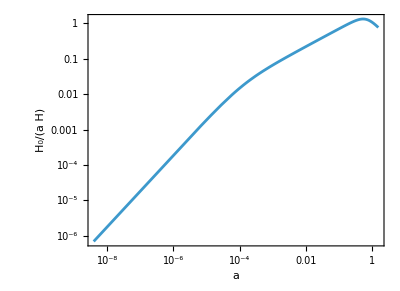

```mathematica
avHplot = ParametricPlot[{aasol[τ],aasol[τ]H00/(dasol[τ]*α)},{τ,τini,0.06},AxesLabel->{"a","H_0/(a H)"}, ScalingFunctions-> {"Log","Log"},PlotRange->All,Frame->True,AxesLabel->{"a","H_0/(a H)"}]
```

```mathematica
VarPiSolutions[[1]]
```

VarPi0+(H0 OmegaM0 tau (stigma-VarPi0^2)^(3/2) ((5-2 stigma) stigma^2+2 stigma (1+(-5+stigma) stigma) VarPi0^2+(-1+4 stigma^2) VarPi0^4) √(-VarPi0^2+stigma (5+4 stigma (-2+VarPi0^2))))/(4 √(OmegaR0 stigma ups2) (stigma^3 (5+stigma) (-1+2 stigma)+3 stigma^2 (8+stigma (-17+3 stigma)) VarPi0^2-stigma (11+stigma+2 stigma^2 (-30+stigma (14+stigma))) VarPi0^4+(-1+2 stigma) (1+2 stigma) (-2+3 (-1+stigma) stigma) VarPi0^6))

```mathematica
aSolutions
```

{-((0.+1.06283 ⅈ) tau √(0.9-VarPi0^2))/(VarPi0 √(-1.98+2.24 VarPi0^2))-(551.25 tau^2 (-0.9+VarPi0^2) (0.5832+0.1458 VarPi0^2-2.97 VarPi0^4+2.24 VarPi0^6))/(VarPi0^2 (3.44088-11.8341 VarPi0^2+13.4782 VarPi0^4-5.0848 VarPi0^6)),(1.06283 tau √(-(0.9-VarPi0^2)/(-1.98+2.24 VarPi0^2)))/VarPi0-(551.25 tau^2 (-0.9+VarPi0^2) (0.5832+0.1458 VarPi0^2-2.97 VarPi0^4+2.24 VarPi0^6))/(VarPi0^2 (3.44088-11.8341 VarPi0^2+13.4782 VarPi0^4-5.0848 VarPi0^6))}